# Trend duration analysis

## Initialization

```mathematica
SeedRandom[Method->"MersenneTwister"];
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];

SignRatio[returns_]:= N[Count[Map[Sign,returns],1]/Length[returns]];
PriceChangeRatio[returns_]:=Total[Select[returns,Positive]]/Total[Abs[returns]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,RGBColor[0.01, 0.61, 0.]};
```

#### Observable definition

```mathematica
SimpleReturns[prices_, lag_:1]:= Drop[prices, lag] - Drop[prices, -lag];
Returns[prices_, lag_:1]:= N[Log[Drop[prices,lag]]-Log[Drop[prices,-lag]]];

FirstSign[returnsSign_]:=Block[{firstSign},
firstSign = First[returnsSign];
If[firstSign ≠ 0,
Return[firstSign]
,
Return[FirstCase[returnsSign,1|-1]]
];
];
FixFirstSign[returnsSign_]:=Block[{result},
result = returnsSign;
result[[1]] = FirstSign[returnsSign];
Return[result]
];
FixAllSigns[returnsSign_]:=FixedPoint[
Flatten[SequenceReplace[#,{x_,0}:>{x,x}]]&,
FixFirstSign[returnsSign]
];

TrendDuration[prices_] := Map[Length, Split[FixAllSigns[Sign[SimpleReturns[prices]]]]];
UpwardTrendDuration[prices_] := Module[{splitted,posTrends},
	splitted = Split[FixAllSigns[Sign[SimpleReturns[prices]]]];
	posTrends = Select[splitted, Apply[And, Positive[#]]&];
	Return[Map[Length, posTrends]];
];
DownwardTrendDuration[prices_] := Module[{splitted,negTrends},
	splitted = Split[FixAllSigns[Sign[SimpleReturns[prices]]]];
	negTrends = Select[splitted, Apply[And, Negative[#]]&];
	Return[Map[Length, negTrends]];
];

TrendReturns[prices_] := Block[{endpoints},
	endpoints = Map[First, TakeList[prices, Append[TrendDuration[prices], All]]];
	Return[Returns[endpoints]];
];

DatedSimpleReturns[dates_, prices_, lag_:1] := Transpose[{Drop[dates, -1], N[Drop[prices, lag] - Drop[prices, -lag]]}];
DatedSimpleReturns[datedprices_, lag_:1] := DatedSimpleReturns[datedprices[[All, 1]], datedprices[[All, 2]], lag];

DatedReturns[dates_, prices_, lag_:1] := Transpose[{Drop[dates, -1], N[Log[Drop[prices, lag]] - Log[Drop[prices, -lag]]]}];
DatedReturns[datedPrices_, lag_:1] := DatedReturns[datedPrices[[All, 1]], datedPrices[[All, 2]], lag];

DatedTrendReturns[dates_, prices_] := Block[{endpoints},
	endpoints = Map[First, TakeList[Transpose[{dates, prices}], Append[TrendDuration[prices], All]]];
	Return[Transpose[{Drop[endpoints[[All,1]], -1], Returns[endpoints[[All, 2]]]}]];
];
DatedTrendDuration[dates_, prices_] := Block[{endpoints,trendDuration},
	trendDuration = TrendDuration[prices];
	endpoints = Map[First, TakeList[dates, Append[trendDuration, All]]];
	Return[Transpose[{Drop[endpoints, -1], trendDuration}]];
];
DatedTrendDuration[datedprices_] := Block[{endpoints,trendDuration},
	trendDuration = TrendDuration[datedprices[[All, 2]]];
	endpoints = Map[First, TakeList[datedprices[[All, 1]], Append[trendDuration, All]]];
	Return[Transpose[{Drop[endpoints, -1], trendDuration}]];
];
```

#### Statistical measures

```mathematica
StandardErrorAvg[data_]:=N[StandardDeviation[data]/(√Length[data])];
StandardErrorStd[data_]:=N[StandardDeviation[data]/(√(2(Length[data]-1)))];
StandardErrorSkw[data_]:=Block[{n = Length[data]},N[√((6n(n-1))/((n-2)(n+1)(n+3)))]];
StandardErrorKurt[data_]:=Block[{n = Length[data]},N[√((n^2-1)/((n-3)(n+5)))]];
MakeStatisticTableRow[data_] := 
{
{"μ",ToString[TraditionalForm[Mean[data]]]<>"±"<>ToString[StandardErrorAvg[data]]},
{"σ", ToString[TraditionalForm[StandardDeviation[data]]]<>"±"<>ToString[StandardErrorStd[data]]},
{"Skewness", ToString[TraditionalForm[Skewness[data]]]<>"±"<>ToString[StandardErrorSkw[data]]},
{"Kurtosis", ToString[TraditionalForm[Kurtosis[data]]]<>"±"<>ToString[StandardErrorKurt[data]]}
};
MakeStatisticTable[marketnames_,dists_] := Module[{gridmm},
gridmm = {Join[{""},marketnames],
Join[{"μ"},Table[ToString[TraditionalForm[Mean[i]]]<>"±"<>ToString[StandardErrorAvg[i]],{i,dists}]],
Join[{"σ"}, Table[ToString[TraditionalForm[StandardDeviation[i]]]<>"±"<>ToString[StandardErrorStd[i]],{i,dists}]],
Join[{"Skewness"}, Table[ToString[TraditionalForm[Skewness[i]]]<>"±"<>ToString[StandardErrorSkw[i]],{i,dists}]],
Join[{"Kurtosis"}, Table[ToString[TraditionalForm[Kurtosis[i]]]<>"±"<>ToString[StandardErrorKurt[i]],{i,dists}]]};
Grid[gridmm,
Alignment->Left,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{LightGray,None},{Gray,None}}
]
];
```

#### Dataset management

```mathematica
SetAttributes[AddToDataset, HoldFirst];
AddToDataset[database_, newkey_, f_, argkeys_]:=
If[!MemberQ[Keys[First[database]], newkey],
	database = Map[Append[#, newkey->Apply[f, Map[#, argkeys]]]&, database],
	
	database = Map[ReplacePart[#, newkey->Apply[f, Map[#, argkeys]]]&, database]
];

SetAttributes[AddKeyToMarket, HoldFirst];
AddKeyToMarket[market_, newkey_, f_, argkeys_]:=
If[!MemberQ[Keys[market], newkey],
	market = Append[market, newkey->Apply[f, Map[market, argkeys]]];
	,
	market = ReplacePart[market, newkey->Apply[f, Map[market, argkeys]]];
];

AddKeyToMarket[market_, newkey_->newvalue_]:=
If[!MemberQ[Keys[market], newkey],
	market = Append[market, newkey->newvalue];
	,
	market = ReplacePart[market, newkey->newvalue];
];
```

### Package information

```mathematica
?AdvancedMapping`*
```

## Dataset

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_NASDAQ_MXX_NIKKEI_datasetV3.wdx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","NASDAQ Composite","IPC","Nikkei 225"};

(* Manual fix for preproccesing error in Nikkei where null values appear in the price. *)
database[[4,"Prices"]] = DeleteCases[database[[4,"Prices"]],"null"];
```

Date fixer: There are no dates in the original dataset, this generates the intermediate dates.

```mathematica
GenerateDaysBetween[firstDate_DateObject,lastDate_DateObject,length_]:=Block[{dayRange,dayCount,ratio},
dayRange = DayRange[firstDate,lastDate];
dayCount = DayCount[firstDate,lastDate];
ratio = dayCount/length;
Table[Part[dayRange,Floor[i*ratio]],{i,length}]
];
AddToDataset[database,"Dates",GenerateDaysBetween[DateObject[#1],DateObject[#2],Length[#3]]&,{"FirstDate","LastDate","Prices"}];
```

```mathematica
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Trend example

Figure. 1

```mathematica
smallSample = Take[database[[2]]["Prices"],50];
smallSampleInTime = Transpose[{Range[50],smallSample}];
smallTr = DatedTrendReturns[Range[50],smallSample];
pricesInTr = smallSampleInTime[[smallTr[[All,1]]]];
```

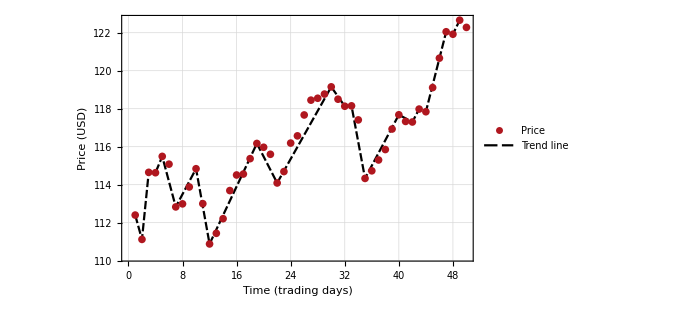

```mathematica
figure = ListPlot[
{smallSampleInTime,pricesInTr},
Joined->{False, True},
ImageSize->500,
PlotTheme->"Monochrome",
FrameLabel->{Style["Time (trading days)",15],Style["Price (USD)",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->colors,
PlotLegends->Placed[LineLegend[{"Price", "Trend line"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
```

## Example of trend duration plot

```mathematica
market = First[database];
durations = TrendDuration[market["Prices"]];
```

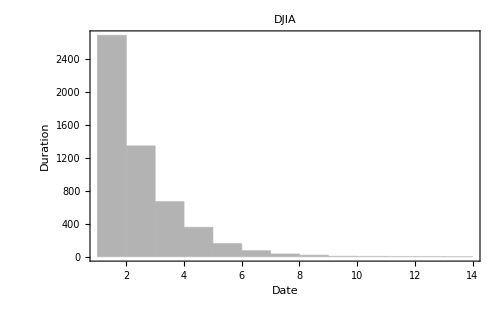

```mathematica
Histogram[
durations,
PlotTheme->"Monochrome", 
Frame->True,
FrameLabel->{Style["Date",15], Style["Duration",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
```

## Efficient market model

```mathematica
market = First[database];
```

```mathematica
Take[market["Prices"],10]
```

{811.85,792.45,827.79,816.96,823.11,814.88,800.07,807.61,803.97,807.09}

```mathematica
DivReturns[prices_]:=Drop[prices,1]/Drop[prices,-1];
PercentageReturns[prices_]:=100*(Drop[prices,1]/Drop[prices,-1]-1) ;
```

```mathematica
Qi = DivReturns[market["Prices"]];
```

```mathematica
FindDistribution[Qi,5]
```

{MixtureDistribution[{0.52721,0.47279},{GammaDistribution[559.31,0.00172616],NormalDistribution[1.05748,0.0292952]}],NormalDistribution[1.00137,0.0584421],NormalDistribution[1.0019,0.0587436],MixtureDistribution[{0.177034,0.822966},{GammaDistribution[1563.82,0.000603856],LogisticDistribution[1.0147,0.0334696]}],StudentTDistribution[1.00899,0.0580625,385.8]}

```mathematica
param = FindDistributionParameters[Qi,LogNormalDistribution[μ,σ]]
```

{μ→0.000333037,σ→0.0111676}

```mathematica
fitted = LogNormalDistribution[μ,σ]/.param
```

LogNormalDistribution[0.000333037,0.0111676]

```mathematica
DistributionFitTest[Qi,fitted]
```

2.22045×10^-16

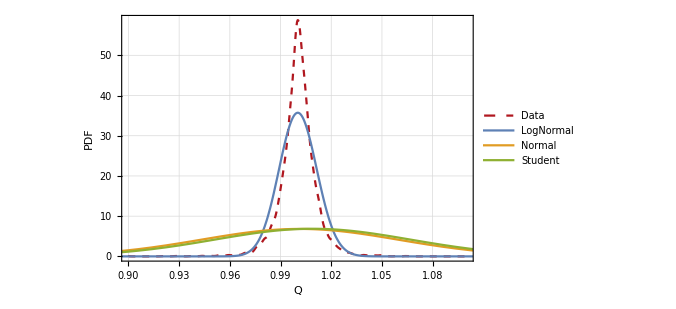

```mathematica
Show[
SmoothHistogram[Qi,
PlotRange->{{0.9,1.1},All},
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Q",15], Style["PDF",15]},
BaseStyle->FontSize->13,
ImageSize->500,
PlotStyle->{Dashed,First[colors]},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
PlotLegends->{"Data"}
],
Plot[
{
PDF[LogNormalDistribution[0.00033303726275681907,0.011167634195248017],x],
PDF[NormalDistribution[1.0013729747050157,0.05844214226527113],x],
PDF[StudentTDistribution[1.0089860632674348,0.05806249824824026,385.80035224172843],x]
},
{x,0.8,1.2},
PlotRange->All,
PlotLegends->{"LogNormal","Normal","Student"}
]
]
```

```mathematica
RandomPriceTS[n_]:=FoldList[Times,1,RandomVariate[LogNormalDistribution[0.00033303726275681907,0.011167634195248017],n]];
```

```mathematica
riskFreeDataset = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","RiskFreeReturn","RiskFreeRet_Database.wdx"}]];
```

Import::nffil: File C:\Users\hp\Documents\Programacion\Datasets\RiskFreeReturn\RiskFreeRet_Database.wdx not found during Import.

Fuente: https://mba.tuck.dartmouth.edu/pages/faculty/ken.french/data_library.html

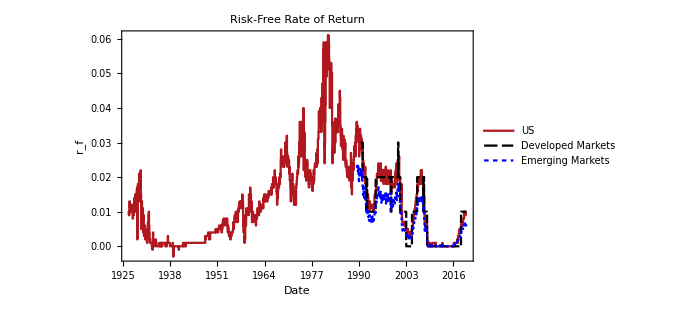

```mathematica
DateListPlot[
riskFreeDataset[[All,"DateReturns"]],
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["r_f",15]},
BaseStyle->FontSize->13,
PlotLabel->"Risk-Free Rate of Return",
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
PlotLegends->Placed[LineLegend[{"US","Developed Markets","Emerging Markets"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}]
]
```

```mathematica
database[[1]]//Keys
```

{Name,FirstDate,LastDate,Prices,Dates}

```mathematica
Flatten[database[[All,"Dates"]]]//Min
```

Day: Mon 30 Oct 1978

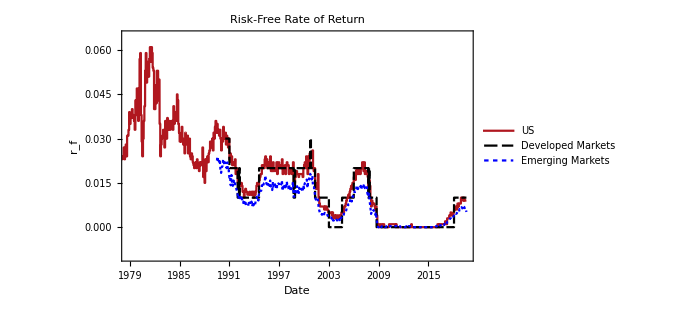

```mathematica
DateListPlot[
riskFreeDataset[[All,"DateReturns"]],
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["r_f",15]},
BaseStyle->FontSize->13,
PlotLabel->"Risk-Free Rate of Return",
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
PlotRange->{{DateObject[{1978,10,30},"Day","Gregorian",-5.],DateObject[{2019,8},"Month","Gregorian",-5.]},{-0.01,0.065}},
PlotLegends->Placed[LineLegend[{"US","Developed Markets","Emerging Markets"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Top}]
]
```

```mathematica
Min[Flatten[riskFreeDataset[[All,"DateReturns"]][[All,All,1]]]]
```

Day: Thu 1 Jul 1926

```mathematica
Table[Min[riskFreeDataset[[All,"DateReturns"]][[i]][[All,1]]],{i,1,3}]
```

{Day: Thu 1 Jul 1926,Day: Mon 2 Jul 1990,Month: Jul 1989}

```mathematica
GetRfRate[date_,type_]:=Block[{usRiskFreeData,devRiskFreeData,emRiskFreeData,correctedDate,result},
usRiskFreeData = riskFreeDataset[[1]];
devRiskFreeData = riskFreeDataset[[2]];
emRiskFreeData = riskFreeDataset[[3]];

correctedDate = date;
If[DayName[date]==Saturday,correctedDate = DatePlus[date,2]];
If[DayName[date]==Sunday,correctedDate = DatePlus[date,1]];

If[correctedDate<DateObject[{1990,7,2},"Day","Gregorian",-5.],correctedDate = DateObject[{1990,7,2},"Day","Gregorian",-5.]];
If[correctedDate>DateObject[{2019,7,31},"Day","Gregorian",-5.],correctedDate =DateObject[{2019,7,31},"Day","Gregorian",-5.]];

If[type == "US",
result = FirstCase[usRiskFreeData["DateReturns"],{correctedDate,x_}:>x]
];
If[type == "Developed",
result = FirstCase[devRiskFreeData["DateReturns"],{correctedDate,x_}:>x]
];
If[type == "Emerging",
correctedDate = DateObject[Take[DateList[correctedDate],2]];
result = FirstCase[emRiskFreeData["DateReturns"],{correctedDate,x_}:>x]
];

If[result ===Missing["NotFound"],
result = GetRfRate[DatePlus[correctedDate,5],type]
];

Return[result];
];
Estimateσ[divReturns_]:=Block[{μ,σ},
σ/.FindDistributionParameters[divReturns,LogNormalDistribution[μ,σ]]
];
Estimateμ[divReturns_]:=Block[{μ,σ},
μ/.FindDistributionParameters[divReturns,LogNormalDistribution[μ,σ]]
];
CalculateQ[{σ_,rf_}]:=1/2+1/2 Erf[σ/(2 √2)-Log[1+rf]/(σ √2)];
CalculateQv2[{μ_,rf_}]:=1/2+1/2 Erf[-μ/(√(4( Log[1+rf]- μ)))];
```

```mathematica
Solve[1+rf ==ⅇ^(μ+σ^2/2),σ,Reals]
```

{{σ→ConditionalExpression[-√(-2 μ+2 Log[1+rf]), rf>-1&&μ≤Log[1+rf]]},{σ→ConditionalExpression[√(-2 μ+2 Log[1+rf]), rf>-1&&μ≤Log[1+rf]]}}

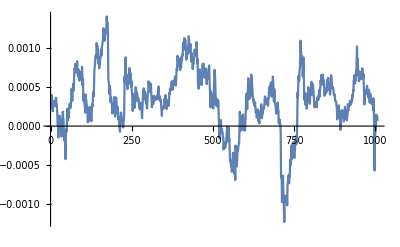

```mathematica
ListLinePlot[Map[Estimateμ,Partition[Qi,504,10]],PlotRange->All]
```

### Estimación de q a partir de la media

```mathematica
EstimateQFromMean[market_,type_]:=Block[{datedPrices,parts,rfs,μs,qs2},
datedPrices =Transpose[{market["Dates"],market["Prices"]}];
parts = Partition[datedPrices,504,10];
rfs = Map[GetRfRate[First[Last[#]],type]&,parts];
μs = Map[Estimateμ[DivReturns[#[[All,2]]]]&,parts];
qs2 = Map[CalculateQv2,Transpose[{μs,rfs}]];

ListLinePlot[qs2,
Frame->True,
PlotRange->{Automatic,{0,0.6}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["q",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
];
```

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

ReplaceAll::reps: {FindDistributionParameters[{0.945963,0.97687,0.951584,1.07156,1.00199,0.986417,1.02276,0.985823,1.00901,0.996338,0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,0.992421,0.991602,1.01263,«7»,0.99721,0.993609,1.00654,1.00774,0.9982,0.98687,0.992873,0.964525,0.99747,0.975783,0.99889,1.00219,1.00455,0.995551,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,«453»},«21»[μ,σ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

ReplaceAll::reps: {FindDistributionParameters[{0.945963,0.97687,0.951584,1.07156,1.00199,0.986417,1.02276,0.985823,1.00901,0.996338,0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,0.992421,0.991602,1.01263,«7»,0.99721,0.993609,1.00654,1.00774,0.9982,0.98687,0.992873,0.964525,0.99747,0.975783,0.99889,1.00219,1.00455,0.995551,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,«453»},«21»[μ,σ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

General::stop: Further output of FindDistributionParameters::ntsprt will be suppressed during this calculation.

ReplaceAll::reps: {FindDistributionParameters[{0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,0.992421,0.991602,1.01263,1.00513,1.01741,0.99323,0.991668,0.997757,0.987508,1.01936,0.99721,0.993609,1.00654,«7»,0.99889,1.00219,1.00455,0.995551,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,1.02704,1.01203,0.992421,0.995067,0.996382,0.963885,0.968879,0.997482,1.00679,1.02153,«453»},«21»[μ,σ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

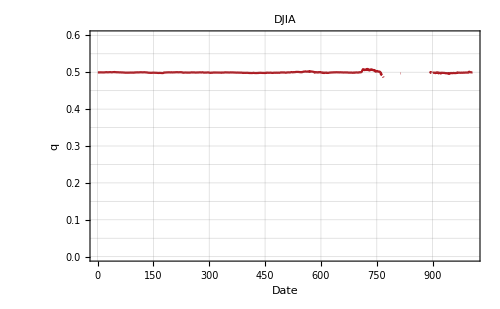
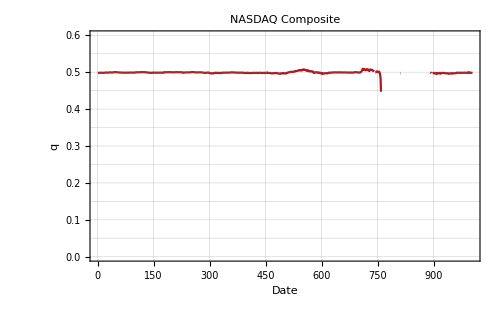
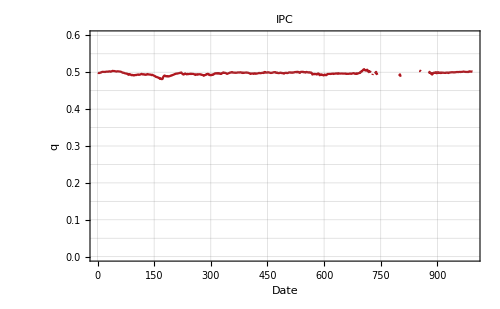
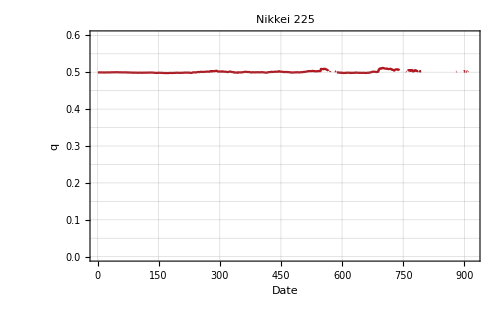

```mathematica
MapThread[EstimateQFromMean,{database,{"US","US","Emerging","Developed"}}]
```

#### Individual

```mathematica
μs = Map[Estimateμ[DivReturns[#[[All,2]]]]&,parts];
qs2 = Map[CalculateQv2,Transpose[{μs,rfs}]];
```

```mathematica
ListLinePlot[qs2,
Frame->True,
PlotRange->{Automatic,{0,0.6}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["q",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
```

-Graphics-

## p-values

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
FQ1[rf_,σ_]:=1/2+ 1/2 Erf[σ/(2 √2)-Log[1+rf]/(σ √2)];
FQ1v2[μ_,rf_]:=1/2+1/2 Erf[-μ/(√(4( Log[1+rf]- μ)))];
```

```mathematica
Solve[1+rf == ⅇ^(μ+σ^2/2),σ,Reals]
```

{{σ→ConditionalExpression[-√(-2 μ+2 Log[1+rf]), rf>-1&&μ≤Log[1+rf]]},{σ→ConditionalExpression[√(-2 μ+2 Log[1+rf]), rf>-1&&μ≤Log[1+rf]]}}

```mathematica
-√(2 (Log[1+rf]-μ))
```

-√2 √(-μ+Log[1+rf])

```mathematica
Plot3D[{FQ1[rf,σ],0.5},{rf,0,0.04},{σ,0,0.3},
AxesLabel->Map[Style[#,15]&,{"r_f","σ","q"}],
PlotStyle->{Opacity[1],Opacity[0.4]},
PlotLegends->{"F_Q(1)","q=0.5"},BoxStyle->{Black},LabelStyle->Black,
BaseStyle->FontSize->13
]
```

-Graphics3D-

```mathematica
Print@Plot3D[{FQ1v2[μ,rf],0.5},{rf,0.001,0.061},{μ,-0.001,0.001},
AxesLabel->Map[Style[#,15]&,{"r_f","μ","q"}],
PlotStyle->{Opacity[1],Opacity[0.4]},
PlotLegends->{"F_Q(1)","q=0.5"},BoxStyle->{Black},LabelStyle->Black,
ImageSize->400,BaseStyle->FontSize->13,
PlotRange->{Automatic,Automatic,{0.495,0.505}}
]
```

-Graphics3D-

Anderson-Darling test for trend durations assuming that the underlying distribution is a GeometricDistribution[p] with p = 0.5.

Figure 4.

```mathematica
CalculateADPiValuesSpecified[dates_,prices_,window_, skip_ :1]:=Module[{datePricesPart,trendDurationParts,ad,lastDates},
datePricesPart = Partition[Transpose[{dates,prices}],window,skip];
trendDurationParts = Map[Apply[DatedTrendDuration,Transpose[#]]&,datePricesPart];
ad = ParallelMap[Quiet[AndersonDarlingTest[#-1,GeometricDistribution[0.5]]] &,trendDurationParts[[All,All,2]]];
lastDates = Map[Last,trendDurationParts[[All,All,1]]];
Return[Transpose[{lastDates,ad}]];
];
```

```mathematica
ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];
FixZeros[{n_,m_}]:=If[m==0,{n,10^-6},{n,m}];

PlotADValues[market_]:=Block[{legend,uppList,plotData,firstDate,lastDate},
If[market["Name"] == "NASDAQ Composite",
legend = Placed[LineLegend[{None,"α = 0.1","α = 0.05","α = 0.01"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}];
,
legend = None
];

{firstDate,lastDate} = {First[First[market["ADValuesSpecified"]]],First[Last[market["ADValuesSpecified"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];

plotData = Join[{market["ADValuesSpecified"]},uppList];

DateListLogPlot[
plotData,
PlotRange->{Automatic,{10^-6,1}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["π-Value",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
Joined->{True,True,True,True,False},
PlotStyle->colors,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->legend,
FrameTicks->True
]
];
EfficiencyPercentage[adValues_,cl_]:=N[Count[adValues,{_,x_} /; x>cl]/Length[adValues]];
EfficiencyTable[database_]:=Block[{efficiencies,formatted},
efficiencies = Table[EfficiencyPercentage[market["ADValuesSpecified"],cl],{market, database},{cl,{0.1,0.05,0.01}}];
formatted = Prepend[MapThread[Prepend[#1,#2]&,{efficiencies,database[[All,"Name"]]}],{"Market/CL","0.1","0.05","0.01"}];
Grid[formatted,Frame->All,Background->{{LightGreen},{LightGray}}]
];
```

### Test if the data fits a GeometricDistribution[p = 0.5], that is, if markets are efficient.

Points below α values indicate the rejection of the null hypothesis D \[Distributed] GeometricDistribution[0.5]

```mathematica
AddToDataset[database,"ADValuesSpecified",CalculateADPiValuesSpecified[#1,#2,504]&,{"Dates","Prices"}];
```

$Aborted

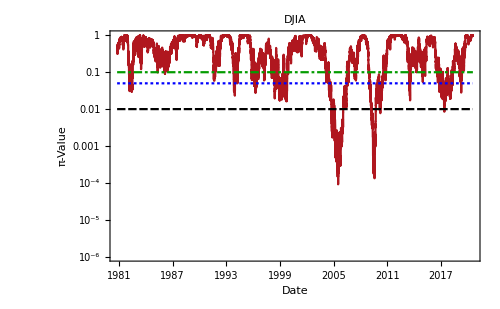
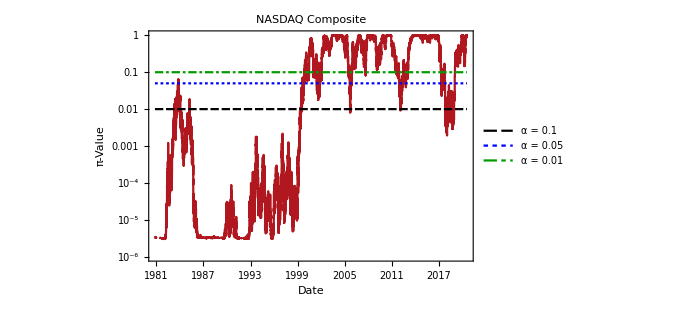
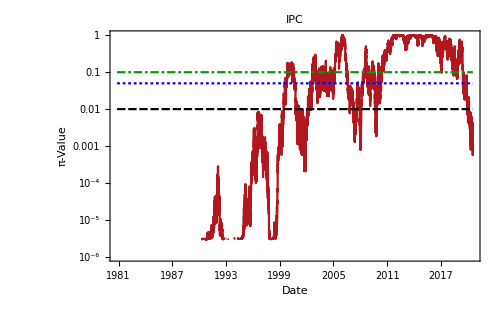
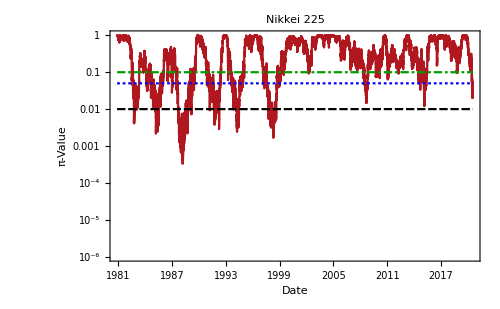

```mathematica
Map[PlotADValues,database]
```

The Anderson-Darling test has been used to quantify the likelihood that a series of trend durations were generated by a process compatible with the EMH model. We can also use this result to assess the efficiency of a given market by looking at the percentage of time that the market behaves as an efficient market. In order to do this we propose the following algorithm:

1- Calculate a time series of π-Values from the sample of trend durations.
2- Count the number of points above the confidence level value.
3- Divide it over the length of the time series to obtain the percentage of time the market has behaved as an efficient market.

By following this procedure we ranked the efficiency of the markets studied in this paper for three confidence levels, 0.1, 0.05 and 0.01. The ranking of efficiency for these markets was consistent for all confidence levels, namely the most efficient market was the DJIA, followed by Nikkei 225, then the NASDAQ Composite and the least efficient market in our sample was the IPC.

```mathematica
EfficiencyTable[database]
```

Market/CL | 0.1 | 0.05 | 0.01
DJIA | 0.790326 | 0.864124 | 0.956694
NASDAQ Composite | 0.424285 | 0.471439 | 0.531851
IPC | 0.29862 | 0.366301 | 0.464599
Nikkei 225 | 0.726141 | 0.813718 | 0.937226

### Dates where markets are not efficient

```mathematica
NotEfficientDates[market_,cl_,window_,skip_]:=Block[{pValues},
pValues = CalculateADPiValuesSpecified[market["Dates"],market["Prices"],window,skip];
Select[pValues,Last[#]<cl&][[All,1]]
];
```

```mathematica
piVs = ProgressTable[CalculateADPiValuesSpecified[database[[i]]["Dates"],database[[i]]["Prices"],100,1],{i,1,Length[database]}];
```

```mathematica
notGeometricDates = Table[Select[piV,Last[#]<0.05&][[All,1]],{piV,piVs}];
```

```mathematica
orderedNGD = Map[Part[notGeometricDates,#]&,{2,3,1,4}];
orderedDatabase = Map[Part[database,#]&,{2,3,1,4}];
```

```mathematica
orderedDatabase[[All,"Name"]]
```

{NASDAQ Composite,IPC,DJIA,Nikkei 225}

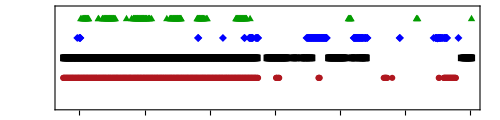

```mathematica
TimelinePlot[orderedNGD,
Frame->True,
PlotLegends->orderedDatabase[[All,"Name"]],
PlotStyle->colors,
PlotTheme->"Monochrome",
BaseStyle->FontSize->13,
ImageSize->500,
PerformanceGoal->"Speed",
PlotMarkers->Automatic,
PlotLayout->"Overlapped"
]
```

```mathematica
orderedDatabase[[1]]//Keys
```

{Name,FirstDate,LastDate,Prices,Dates,ADValuesSpecified}

```mathematica
SeparateEfficientAndNotEfficient[market_,notGeometricDates_,returnType_]:=Block[{datedReturns,efficientReturns,notEfficientReturns},
datedReturns = Transpose[{Drop[market["Dates"],1],returnType[market["Prices"]]}];
efficientReturns = Select[datedReturns,MemberQ[notGeometricDates,First[#]]&][[All,2]];
notEfficientReturns = Select[datedReturns,!MemberQ[notGeometricDates,First[#]]&][[All,2]];

<|"Efficient"->efficientReturns,"NotEfficient"->notEfficientReturns|>
];
```

```mathematica
PlotEfficientVsNotEfficient[market_,notGeometricDates_,returnType_]:=Block[{separated,efficientHistogram,notEfficientHistogram,descriptiveStatisticsTable},
separated = SeparateEfficientAndNotEfficient[market,notGeometricDates,returnType];

efficientHistogram = SmoothHistogram[
separated["Efficient"],
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->Automatic,
PlotStyle->First[colors],
PlotLabel->"Efficient"
];
notEfficientHistogram = SmoothHistogram[separated["NotEfficient"],
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->Automatic,
PlotStyle->First[colors],
PlotLabel->"Not Efficient"
];
descriptiveStatisticsTable = Grid[
Prepend[
Map[Append[First[#],Last[Last[#]]]&,Transpose[{MakeStatisticTableRow[separated["Efficient"]],MakeStatisticTableRow[separated["NotEfficient"]]}]],{"","Efficient","NotEfficient"}
],
Alignment->Left,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{LightBlue,None},{Green,None}}
];

Labeled[Column[{Row[{efficientHistogram,notEfficientHistogram}],descriptiveStatisticsTable}],market["Name"],Top]
];
```

```mathematica
MeanWithError[data_]:=ToString[TraditionalForm[Mean[data]]]<>"±"<>ToString[StandardErrorAvg[data]];
```

```mathematica
AverageReturnByEfficiency[market_,cl_,window_,skip_, avgFunction_ : MeanWithError]:=Block[{ned,separated},
ned = NotEfficientDates[market,cl,window,skip];
separated = SeparateEfficientAndNotEfficient[market,ned,PercentageReturns];

Map[avgFunction,{separated["Efficient"],separated["NotEfficient"]}]
];
```

### Returns by efficiency

#### Comparing window sizes

```mathematica
ProgressMap[
Labeled[
Grid[
Prepend[ProgressTable[Prepend[AverageReturnByEfficiency[database[[j]],0.05,#,1],database[[j,"Name"]]],{j,1,Length[database]},"Label"->"Evaluating market"],{"Market","Efficient μ", "Not Efficient μ"}]
],
#,Top
]&,
{25,50,100,200,300,400},
"Label"->"Evaluating window"
]
```

{Market | Efficient μ | Not Efficient μ
DJIA | -0.046755±0.0511328 | 0.0433168±0.0110405
NASDAQ Composite | -0.0870561±0.0569768 | 0.0599452±0.0132377
IPC | -0.0168893±0.0815113 | 0.128819±0.017088
Nikkei 225 | -0.0128976±0.0673878 | 0.02346±0.013631125,Market | Efficient μ | Not Efficient μ
DJIA | 0.0261173±0.0495009 | 0.0400391±0.0110474
NASDAQ Composite | -0.0673782±0.0447655 | 0.0620825±0.0134592
IPC | -0.0234348±0.0695489 | 0.134446±0.0170878
Nikkei 225 | -0.101572±0.0626344 | 0.0269797±0.013664550,Market | Efficient μ | Not Efficient μ
DJIA | -0.0462905±0.0450368 | 0.0434204±0.0110958
NASDAQ Composite | -0.0962911±0.0323637 | 0.071778±0.0139455
IPC | 0.0299284±0.0524987 | 0.133895±0.0176068
Nikkei 225 | -0.0688389±0.0609905 | 0.0266191±0.0136921100,Market | Efficient μ | Not Efficient μ
DJIA | -0.0176419±0.038462 | 0.0429864±0.0112075
NASDAQ Composite | -0.0605415±0.0238792 | 0.0755094±0.014742
IPC | 0.0127237±0.0448107 | 0.143975±0.0179713
Nikkei 225 | -0.0466558±0.0595574 | 0.0261816±0.0137043200,Market | Efficient μ | Not Efficient μ
DJIA | 0.0105235±0.0556199 | 0.0414877±0.0108899
NASDAQ Composite | -0.0345286±0.0241988 | 0.0744011±0.0149528
IPC | 0.0267824±0.0421486 | 0.143144±0.0181988
Nikkei 225 | -0.0163359±0.0469278 | 0.0253797±0.013937300,Market | Efficient μ | Not Efficient μ
DJIA | 0.00747903±0.0561274 | 0.0417017±0.010876
NASDAQ Composite | -0.0306151±0.023043 | 0.0744567±0.0151305
IPC | 0.0194819±0.0396999 | 0.147142±0.0185108
Nikkei 225 | -0.0383063±0.0450777 | 0.0280249±0.0139881400}

#### Comparing window and confidence level sizes

```mathematica
MarketAverageReturnByEfficiency[cl_,window_,skip_]:=Block[{evalByMarket},
evalByMarket = Table[AverageReturnByEfficiency[database[[j]],cl,window,skip,Mean],{j,1,Length[database]}];
Association[Thread[{"Efficient","NotEfficient"}->Map[Mean,Transpose[evalByMarket]]]]
];
```

```mathematica
avgReturnsByWindowAndCL = Flatten[ProgressTable[{window,cl,MarketAverageReturnByEfficiency[cl,window,10]},{window,25,400,10},{cl,0.01,0.2,0.025}],1];
```

```mathematica
effPts = MapAt[#["Efficient"]&,avgReturnsByWindowAndCL,{All,3}];
```

```mathematica
notEffPts = MapAt[#["NotEfficient"]&,avgReturnsByWindowAndCL,{All,3}];
```

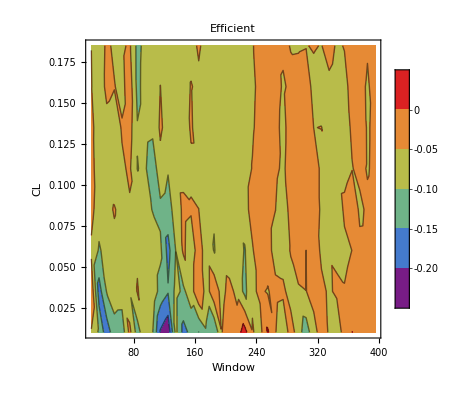

```mathematica
ListContourPlot[effPts,
PlotRange->All,
PlotLegends->Automatic,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->400,
FrameLabel->{Style["Window",15], Style["CL",15]},
ColorFunction->"Rainbow",
PlotLabel->"Efficient"
]
```

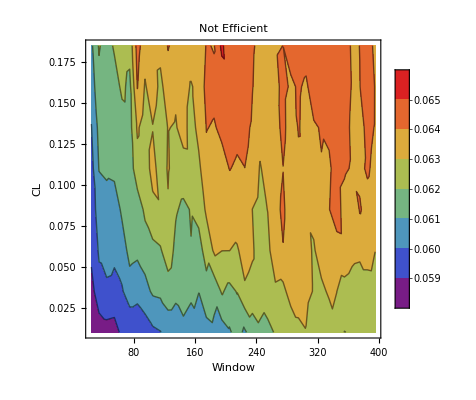

```mathematica
ListContourPlot[notEffPts,
PlotRange->All,
PlotLegends->Automatic,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->400,
FrameLabel->{Style["Window",15], Style["CL",15]},
ColorFunction->"Rainbow",
PlotLabel->"Not Efficient"
]
```

### Percentage returns

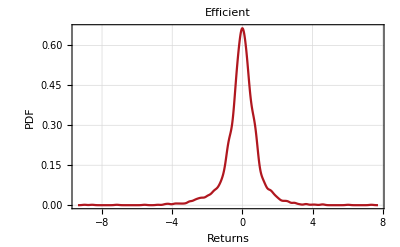
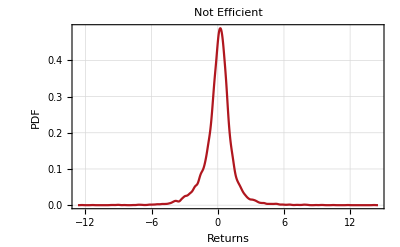
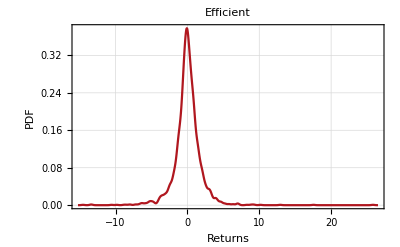
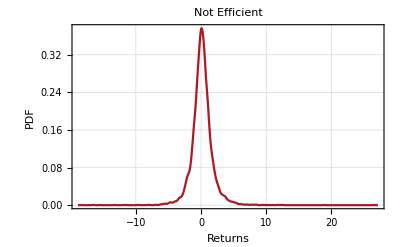
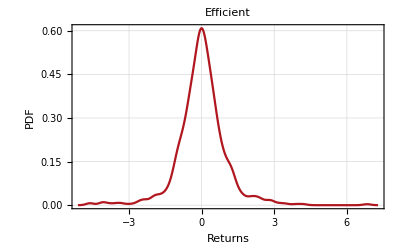
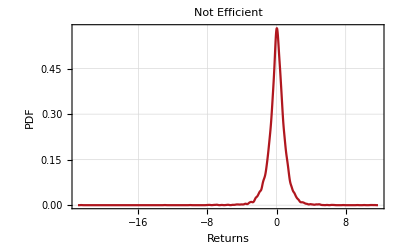
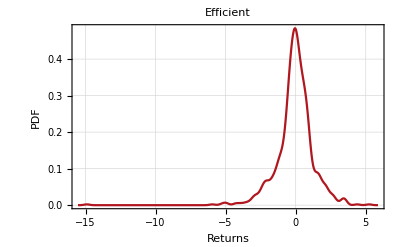
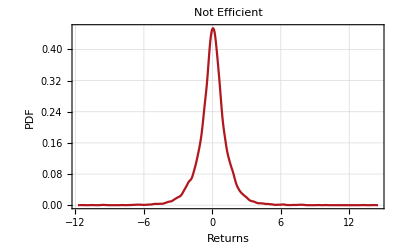
{-Graphics--Graphics-
 | Efficient | NotEfficient
μ | -0.0426064±0.0212834 | 0.0781529±0.0153402
σ | 1.01046±0.0150529 | 1.39579±0.0108478
Skewness | -0.8179±0.0515596 | -0.0976251±0.0269158
Kurtosis | 13.3004±0.999558 | 11.9892±0.999879NASDAQ Composite,-Graphics--Graphics-
 | Efficient | NotEfficient
μ | 0.0274033±0.0374155 | 0.148092±0.0187989
σ | 1.89678±0.0264619 | 1.66676±0.0132937
Skewness | 0.82724±0.0482898 | 0.436683±0.0276219
Kurtosis | 25.6506±0.999612 | 23.5619±0.999873IPC,-Graphics--Graphics-
 | Efficient | NotEfficient
μ | 0.00701486±0.0373468 | 0.0419665±0.0112606
σ | 1.01663±0.026426 | 1.11639±0.00796283
Skewness | 0.108937±0.0898028 | -0.944061±0.0247033
Kurtosis | 8.93273±0.998666 | 31.3058±0.999898DJIA,-Graphics--Graphics-
 | Efficient | NotEfficient
μ | -0.0502281±0.0431652 | 0.0294094±0.0140477
σ | 1.32834±0.0305385 | 1.35849±0.00993374
Skewness | -1.75475±0.079472 | 0.0569441±0.0253252
Kurtosis | 20.6659±0.998953 | 10.4769±0.999893Nikkei 225}

```mathematica
MapThread[PlotEfficientVsNotEfficient[#1,#2,PercentageReturns]&,{orderedDatabase,orderedNGD}]
```

### Log returns

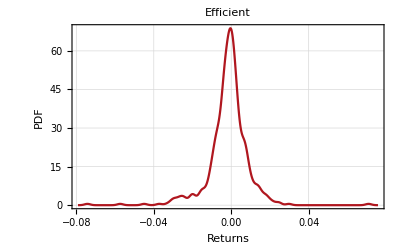
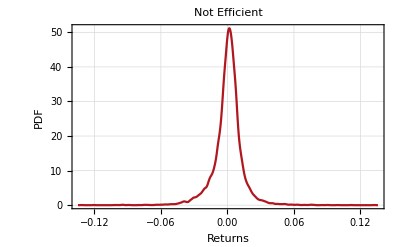
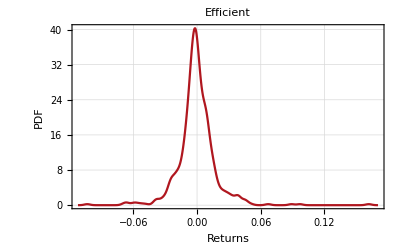
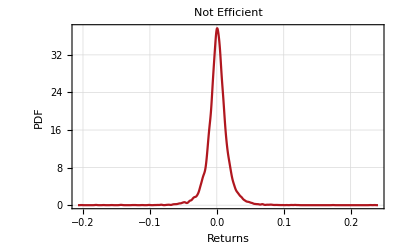
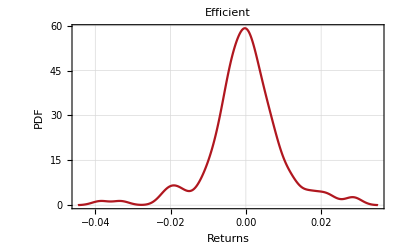
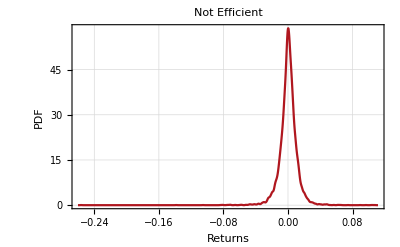
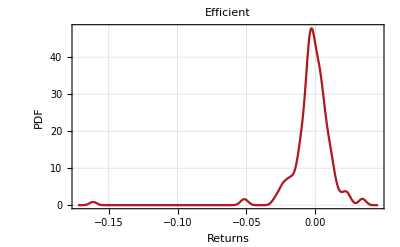
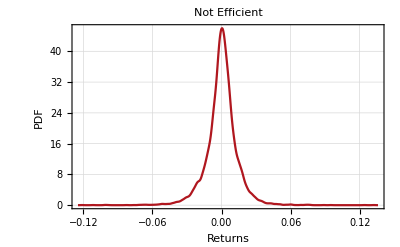
{-Graphics--Graphics-
 | Efficient | NotEfficient
μ | -0.00148205±0.000450199 | 0.000536443±0.000133811
σ | 0.0103448±0.000318641 | 0.0133845±0.0000946237
Skewness | -0.753838±0.106299 | -0.371984±0.0244851
Kurtosis | 14.1595±0.998136 | 12.55±0.9999NASDAQ Composite,-Graphics--Graphics-
 | Efficient | NotEfficient
μ | -0.00030168±0.000725775 | 0.00112015±0.000173255
σ | 0.0181879±0.00051361 | 0.017154±0.000122516
Skewness | 1.10329±0.0975129 | -0.0928576±0.024736
Kurtosis | 17.3001±0.998429 | 22.6614±0.999898IPC,-Graphics--Graphics-
 | Efficient | NotEfficient
μ | -0.000166817±0.000830082 | 0.000339553±0.000109514
σ | 0.00968034±0.000589127 | 0.0111865±0.0000774417
Skewness | -0.359748±0.207774 | -1.44968±0.0239766
Kurtosis | 5.86527±0.993097 | 40.339±0.999904DJIA,-Graphics--Graphics-
 | Efficient | NotEfficient
μ | -0.00264668±0.00124736 | 0.000177885±0.000134317
σ | 0.0166885±0.000884491 | 0.0135121±0.0000949813
Skewness | -4.98358±0.181574 | -0.151235±0.0243456
Kurtosis | 47.7288±0.994675 | 10.0157±0.999901Nikkei 225}

```mathematica
MapThread[PlotEfficientVsNotEfficient[#1,#2,Returns]&,{orderedDatabase,orderedNGD}]
```

### Test if the data fits a GeometricDistribution[p] with any value of p

#### Bootstrap method

```mathematica
MDLMeasureP[sample_]:=N[Length[sample]/Total[sample]];
F0[k_,p_]:=CDF[GeometricDistribution[p],k-1];
Fn[k_,empirical_]:=N[CDF[empirical,k]];
p0[k_,p_]:=F0[k,p]-F0[k-1,p];

AndersonDarlingGeometric[sample_]:=Block[{empiricalD,mdlP},
empiricalD = EmpiricalDistribution[sample];
mdlP = MDLMeasureP[sample];
Length[sample]*Sum[((Fn[k,empiricalD]-F0[k,mdlP])^2 p0[k,mdlP])/(F0[k,mdlP](1-F0[k,mdlP])),{k,1,Max[sample]}]
];
ReplicateSample[sample_,replications_]:=Block[{n,mdlP},
n = Length[sample];
mdlP = MDLMeasureP[sample];

Table[RandomVariate[GeometricDistribution[mdlP],n]+1,replications]
];
ADStatistic[sample_,repetitions_]:=Sort[Map[AndersonDarlingGeometric,ReplicateSample[sample,repetitions]]];
ADStatisticFamilyPValue[sample_,repetitions_ :1000]:=Block[{adStatistic},
adStatistic = Sort[Map[AndersonDarlingGeometric,ReplicateSample[sample,repetitions]]];
CDF[EmpiricalDistribution[adStatistic],AndersonDarlingGeometric[sample]]
];
```

#### Example

```mathematica
market = First[database];
sample = Take[TrendDuration[market["Prices"]],504];
```

```mathematica
MDLMeasureP[sample]
```

0.502994

```mathematica
adStatistic = Sort[Map[AndersonDarlingGeometric,ReplicateSample[sample,10000]]];
```

```mathematica
measuredAD = AndersonDarlingGeometric[sample]
```

0.459565

```mathematica
plt1 = SmoothHistogram[
adStatistic,
PlotRange->{{-0.1,3},All},
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["OverHat[A_n]",15], Style["PDF",15]},
BaseStyle->FontSize->13,
ImageSize->500,
PlotStyle->First[colors],
FrameTicks->True,
GridLines->{{measuredAD},None}
];
plt2 = SmoothHistogram[
adStatistic,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["OverHat[A_n]",15], Style["PDF",15]},
BaseStyle->FontSize->13,
ImageSize->500,
FrameTicks->True,
PlotRange->{{0,measuredAD},Automatic},
PlotStyle->{Thickness[0],First[colors]},
Filling->Axis,
FillingStyle->LightGray
];
```

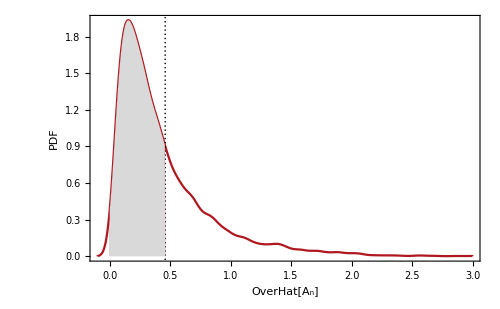

```mathematica
Show[plt1,plt2]
```

```mathematica
ADStatisticFamilyPValue[sample,5000]
```

0.6694

```mathematica
CalculateADPiValuesFamily[market_,window_,skip_ :1]:=Module[{datePricesPart,trendDurationParts,ad,lastDates},
datePricesPart = Partition[Transpose[{market["Dates"],market["Prices"]}],window,skip];
trendDurationParts = Map[Apply[DatedTrendDuration,Transpose[#]]&,datePricesPart];
ad = ProgressParallelMap[ADStatisticFamilyPValue,trendDurationParts[[All,All,2]]];
lastDates = Map[Last,trendDurationParts[[All,All,1]]];
Return[Transpose[{lastDates,ad}]];
];
PlotADPiValuesFamily[market_,piV_]:=Block[{legend,firstDate,lastDate,uppList,plotData},
If[market["Name"] == "NASDAQ Composite",
legend = Placed[LineLegend[{None,"α = 0.1","α = 0.05","α = 0.01"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}];
,
legend = None
];

{firstDate,lastDate} = {First[First[piV]],First[Last[piV]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];

plotData = Join[{piV},uppList];

DateListLogPlot[
plotData,
PlotRange->{Automatic,{10^-4,1}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["π-Value",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
Joined->{True,True,True,True,False},
PlotStyle->colors,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->legend,
FrameTicks->True
]
];
```

```mathematica
piVs = ProgressTable[CalculateADPiValuesFamily[database[[i]],504,15],{i,1,Length[database]},"Label"->"Evaluating markets"];
```

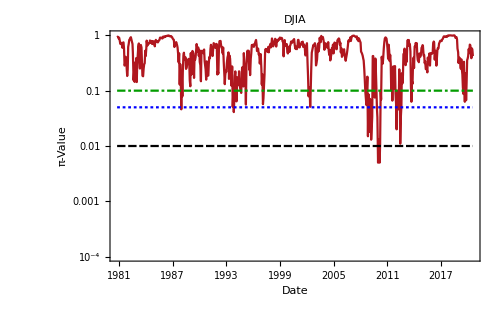
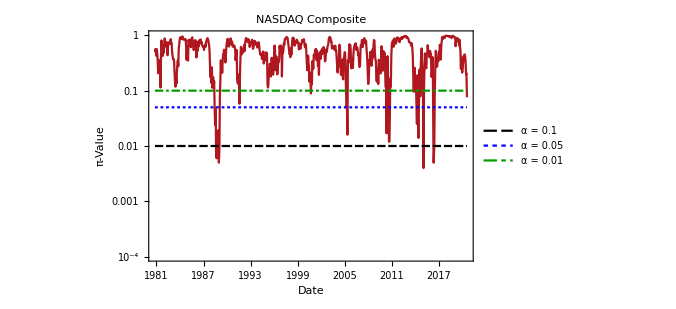
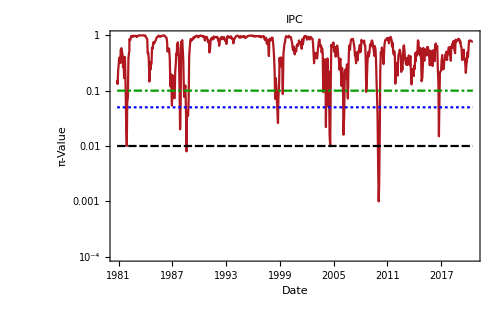
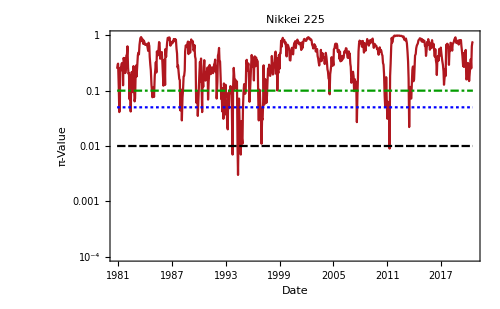

```mathematica
MapThread[PlotADPiValuesFamily,{database,piVs}]
```

```mathematica
notGeometricDates = Table[Select[piV,Last[#]<0.05&][[All,1]],{piV,piVs}];
```

```mathematica
orderedNGD = Map[Part[notGeometricDates,#]&,{2,3,1,4}];
orderedDatabase = Map[Part[database,#]&,{2,3,1,4}];
```

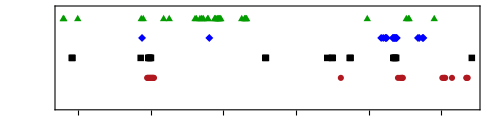

```mathematica
TimelinePlot[
orderedNGD,
Frame->True,
PlotLegends->orderedDatabase[[All,"Name"]],
PlotStyle->colors,
PlotTheme->"Monochrome",
BaseStyle->FontSize->13,
ImageSize->500,
PerformanceGoal->"Speed",
PlotMarkers->Automatic,
PlotLayout->"Overlapped"
]
```

## Distribution

Figure 3.

```mathematica
UpwardTrendDuration[prices_] := Module[{splitted,posTrends},
splitted =Split[Sign[SimpleReturns[prices]]];
posTrends = Select[splitted,Apply[Or,Positive[#]]&];
Return[Map[Length,posTrends]];
];
DownwardTrendDuration[prices_] := Module[{splitted,negTrends},
splitted =Split[Sign[SimpleReturns[prices]]];
negTrends = Select[splitted,Apply[Or,Negative[#]]&];
Return[Map[Length,negTrends]];
];
TrendHistogramPoints[prices_,durationFunction_]:=Module[{trendDuration,histogramList},
trendDuration = durationFunction[prices] - 1;
histogramList = Map[{#,Count[trendDuration,#]/Length[trendDuration]}&,DeleteDuplicates[trendDuration]];
Return[histogramList];
];

EstimateP[trendDuration_]:=N[1/(1+Mean[trendDuration])];
EstimateP[prices_,durationFunction_]:=EstimateP[durationFunction[prices] - 1];
```

PStandardError represents the estimate of the standard error associated with the parameter estimate. The reciprocal of minus the second derivative of the log of the likelihood evaluated at the maximum likelihood estimate of σ obtains the estimate of the variance. To get the standard error one takes the square root of that. The following is the derivation of the formula:
-Graphics-

```mathematica
PLogLikelihood[trendDuration_]:=Block[{p},LogLikelihood[GeometricDistribution[p],trendDuration]];
PStandardError[trendDuration_]:=Block[{p,derivative},
derivative = -1/(D[PLogLikelihood[trendDuration],{p,2}]);
Sqrt[derivative /.p->EstimateP[trendDuration]]
];

GoodnessOfFit[prices_,durationFunction_]:=DistributionFitTest[durationFunction[prices]-1,GeometricDistribution[EstimateP[prices,durationFunction]]];

ChiSquareOverNDFValue[prices_,durationFunction_]:=PearsonChiSquareTest[durationFunction[prices]-1,GeometricDistribution[EstimateP[prices,durationFunction]],{"TestStatistic","DegreesOfFreedom"}];

FitTrend[prices_,durationFunction_]:=Module[{trendDuration,p,fittedPts},
trendDuration = durationFunction[prices] - 1;
p = EstimateP[trendDuration];
fittedPts = Table[{k,PDF[GeometricDistribution[p],k]},{k,0,Max[trendDuration]}];
Return[fittedPts];
];

PlotTrendDistribution[trendDatabase_,direction_,color_]:=Block[{fit,histogram,estimatedP,ref,legend,error,errorUpperFit,errorLowerFit},
fit = If[direction=="Upward","UpwardFit","DownwardFit"];
histogram = If[direction=="Upward","UpwardHistogram","DownwardHistogram"];
estimatedP = If[direction=="Upward","UpwardEstimatedP","DownwardEstimatedP"];
ref = GenerateFitted[0.5,Max[trendDatabase[histogram][[All,1]]]];

If[trendDatabase["Name"] == "DJIA",
legend = Placed[
LineLegend[{"Fit","Histogram","p̂ = 0.5","Lower bound of fit","Upper bound of fit"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
{Left,Bottom}
];
,
legend = None
];

If[direction == "Upward",
error = PStandardError[UpwardTrendDuration[trendDatabase["Prices"]]-1];
,
error = PStandardError[DownwardTrendDuration[trendDatabase["Prices"]]-1];
];

errorUpperFit = GenerateFitted[trendDatabase[estimatedP]+error,Max[trendDatabase[histogram][[All,1]]]];
errorLowerFit = GenerateFitted[trendDatabase[estimatedP]-error,Max[trendDatabase[histogram][[All,1]]]];

ListLogPlot[
{trendDatabase[fit],trendDatabase[histogram],ref,errorLowerFit,errorUpperFit},
Joined->{True,False, True,True,True},
Filling->{4->{5}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Duration (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->trendDatabase["Name"],
PlotStyle->{color,{PointSize[Large],Black},Gray,RGBColor[0., 0.47000000000000003, 0.55],RGBColor[0., 0.84, 0.23]},
Epilog->{Inset[Framed[Text[Style["p̂ = "<>ToString[trendDatabase[estimatedP]]<>"±"<>ToString[error],14]],RoundingRadius->1,Background->RGBColor[1,1,1,.8]],Scaled[{0.7,.8}]]},
ImageSize->500,
PlotLegends->legend,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
];
PlotTrendDistribution[trendDatabase_,color_]:=Block[{fit,histogram,estimatedP,ref,legend,error,errorUpperFit,errorLowerFit},
fit = "AllFit";
histogram = "AllHistogram";
estimatedP = "AllEstimatedP";
ref = GenerateFitted[0.5,Max[trendDatabase[histogram][[All,1]]]];

If[trendDatabase["Name"] == "DJIA",
legend = Placed[
LineLegend[{"Fit","Histogram","p̂ = 0.5","Lower bound of fit","Upper bound of fit"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
{Left,Bottom}
];
,
legend = None
];

error = PStandardError[TrendDuration[trendDatabase["Prices"]]-1];
errorUpperFit = GenerateFitted[trendDatabase[estimatedP]+error,Max[trendDatabase[histogram][[All,1]]]];
errorLowerFit = GenerateFitted[trendDatabase[estimatedP]-error,Max[trendDatabase[histogram][[All,1]]]];

ListLogPlot[
{trendDatabase[fit],trendDatabase[histogram],ref,errorLowerFit,errorUpperFit},
Joined->{True,False, True,True,True},
Filling->{4->{5}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Duration (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->trendDatabase["Name"],
PlotStyle->{color,{PointSize[Large],Black},Gray,RGBColor[0., 0.47000000000000003, 0.55],RGBColor[0., 0.84, 0.23]},
Epilog->{Inset[Framed[Text[Style["p̂ = "<>ToString[trendDatabase[estimatedP]]<>"±"<>ToString[error],14]],RoundingRadius->1,Background->RGBColor[1,1,1,.8]],Scaled[{0.7,.8}]]},
ImageSize->500,
PlotLegends->legend,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
];
```

```mathematica
RandomPPlusQ[n_]:=Block[{prices},
prices = RandomPriceTS[n];
EstimateP[prices,UpwardTrendDuration]+EstimateP[prices,DownwardTrendDuration]
];
```

```mathematica
pPlusQStatistic = ProgressTable[RandomPPlusQ[10000],10000];
```

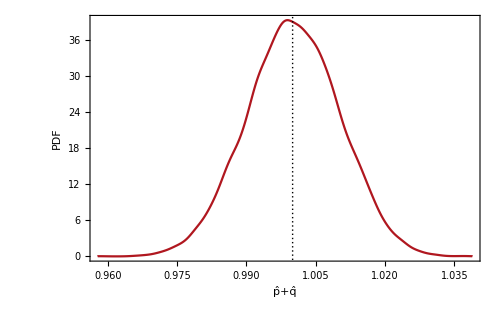

```mathematica
SmoothHistogram[pPlusQStatistic,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["p̂+q̂",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{1},{}},
PlotStyle->First[colors]
]
```

All trends

```mathematica
AddToDataset[database,"AllHistogram",TrendHistogramPoints[#,TrendDuration]&,{"Prices"}];
AddToDataset[database,"AllFit",FitTrend[#,TrendDuration]&,{"Prices"}];
AddToDataset[database,"AllEstimatedP",EstimateP[#,TrendDuration]&,{"Prices"}];
AddToDataset[database,"AllGoodnessFit",GoodnessOfFit[#,TrendDuration]&,{"Prices"}];
AddToDataset[database,"AllChiSquare",ChiSquareOverNDFValue[#,TrendDuration]&,{"Prices"}];
```

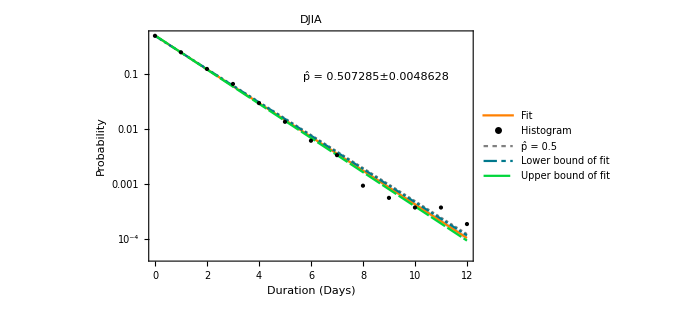
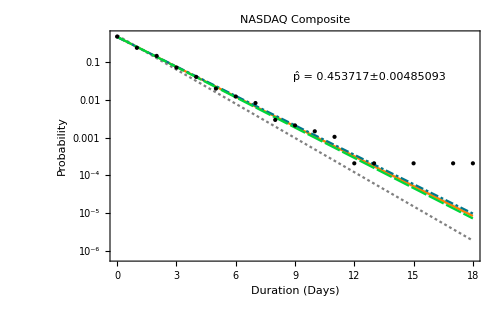
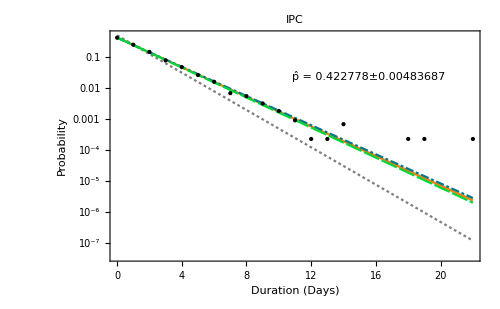
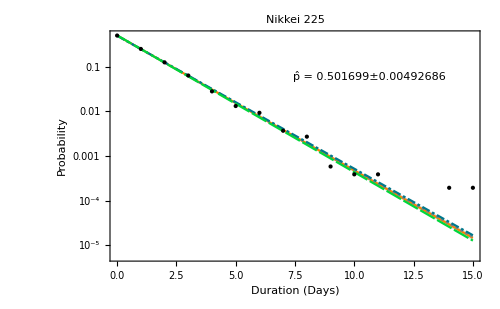

```mathematica
Map[PlotTrendDistribution[#,Orange]&,database]
```

```mathematica
Dataset@database[[All,{"Name","UpwardGoodnessFit"}]]
```

```mathematica
Dataset@database[[All,{"Name","UpwardChiSquare"}]]
```

Upward trends

```mathematica
AddToDataset[database,"UpwardHistogram",TrendHistogramPoints[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardFit",FitTrend[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardEstimatedP",EstimateP[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardGoodnessFit",GoodnessOfFit[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardChiSquare",ChiSquareOverNDFValue[#,UpwardTrendDuration]&,{"Prices"}];
```

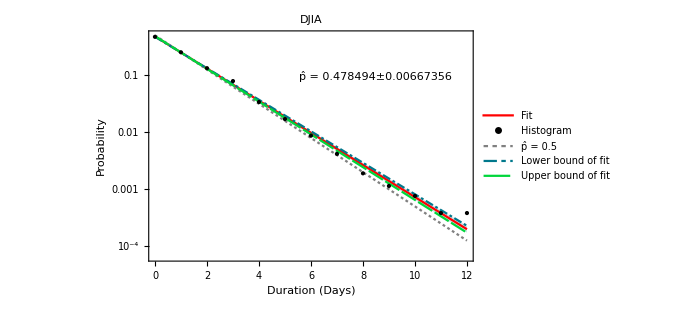
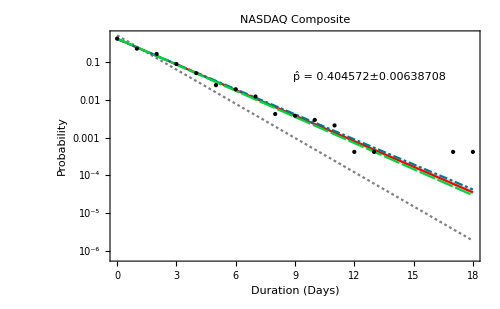
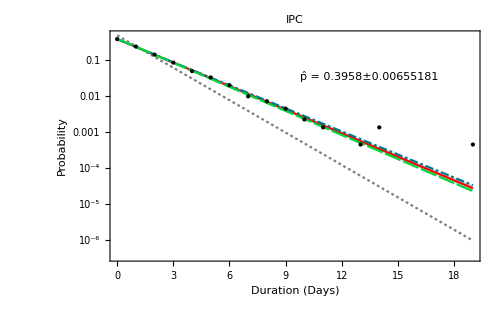
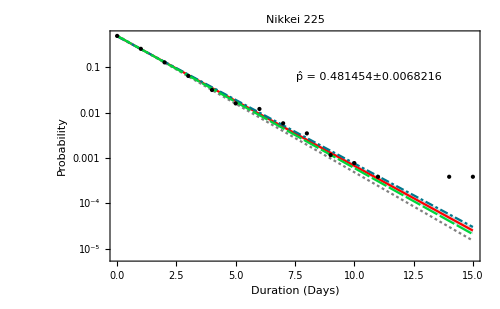

```mathematica
Map[PlotTrendDistribution[#,"Upward",Red]&,database]
```

```mathematica
Dataset@database[[All,{"Name","UpwardGoodnessFit"}]]
```

```mathematica
Dataset@database[[All,{"Name","UpwardChiSquare"}]]
```

Downward trends

```mathematica
AddToDataset[database,"DownwardHistogram",TrendHistogramPoints[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardFit",FitTrend[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardEstimatedP",EstimateP[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardGoodnessFit",GoodnessOfFit[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardChiSquare",ChiSquareOverNDFValue[#,DownwardTrendDuration]&,{"Prices"}];
```

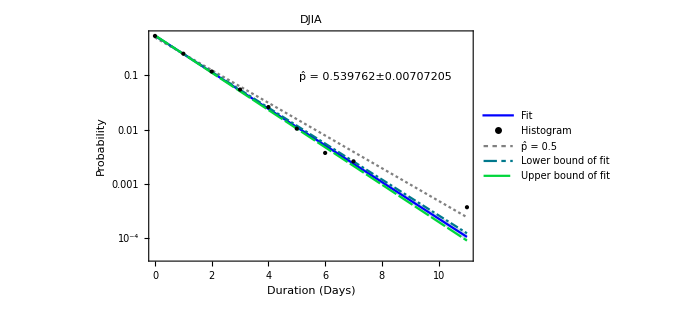
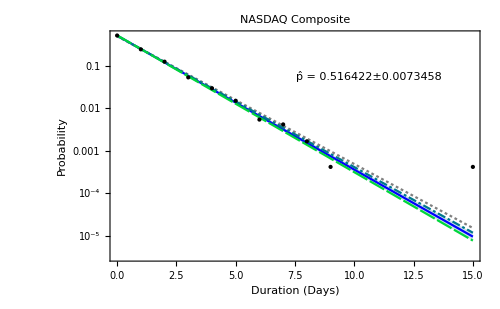
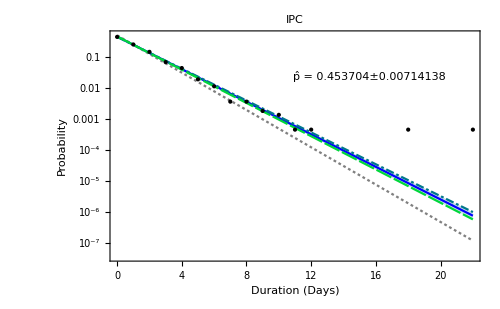
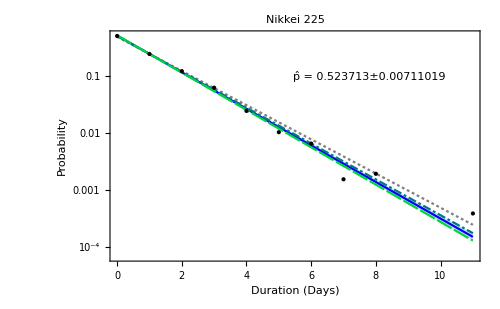

```mathematica
Map[PlotTrendDistribution[#,"Downward",Blue]&,database]
```

```mathematica
Dataset@database[[All,{"Name","DownwardGoodnessFit"}]]
```

```mathematica
Dataset@database[[All,{"Name","DownwardChiSquare"}]]
```

## Trend sign

Figure. 2.

```mathematica
SignChangeInTime[prices_,window_,skip_:1]:=Module[{returns,part,ratios},
returns = Returns[prices];
part = Partition[returns,window,skip];
ratios = Map[SignRatio,part];
Return[ratios];
];
```

```mathematica
AddToDataset[database,"PriceChangeRatio",SignChangeInTime[#,504,5]&,{"Prices"}];
```

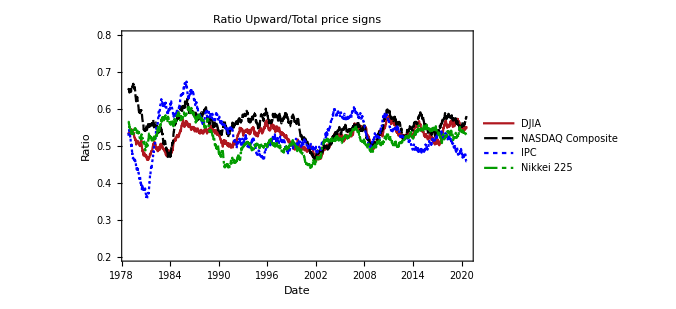

```mathematica
DateListPlot[
database[[All,"PriceChangeRatio"]],
{First[database]["FirstDate"],First[database]["LastDate"]},
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"Ratio Upward/Total price signs",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.8}},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
```

## Samples size

```mathematica
GetInfo[market_]:=Module[{name,sampleSize,partitionSize,firstDate, lastDate},
name = market["Name"];
sampleSize = Length[market["Prices"]];
partitionSize = Length[Partition[TrendDuration[market["Prices"]],504,1]];
firstDate = DateString[market["FirstDate"],"ISODate"];
lastDate = DateString[market["LastDate"],"ISODate"];

Return[{name,sampleSize,partitionSize, firstDate,lastDate}];
];
```

```mathematica
info = Map[GetInfo,database];
Grid[Join[{{"Market name","Sample size","Partition size","First date","Last date"}},info],Background->{None,{Gray}}]
```

Market name | Sample size | Partition size | First date | Last date
DJIA | 10571 | 4859 | 1978-10-30 | 2020-08-07
NASDAQ Composite | 10534 | 4276 | 1978-10-30 | 2020-08-07
IPC | 10432 | 3907 | 1978-10-30 | 2020-08-07
Nikkei 225 | 10300 | 4664 | 1978-10-30 | 2020-08-07

## Parameter estimation

TODO: Obtener los histogramas de p y q con la tabla de media, varianza, etc

```mathematica
UpwardDatedTrendDuration[prices_] := Module[{simpleReturns,splitted,posTrends,result},
simpleReturns = SimpleReturns[prices];
splitted =Split[Map[Sign,simpleReturns]];
posTrends = Select[splitted,Apply[Or,Positive[#]]&];
result = Map[Length,posTrends];
Return[result];
];
UpwardDatedTrendDuration[dates_,prices_] := Module[{simpleReturns,splitted,posTrends,result},
simpleReturns = DatedSimpleReturns[dates,prices];
splitted =SplitBy[MapAt[Sign,simpleReturns,{All,2}],Last];
posTrends = Select[splitted,Apply[Or,Positive[#[[All,2]]]]&];
result = Map[{#[[1,1]],Length[#]}&,posTrends];
Return[result];
];
DownwardDatedTrendDuration[prices_] := Module[{simpleReturns,splitted,posTrends,result},
simpleReturns = SimpleReturns[prices];
splitted =Split[Map[Sign,simpleReturns]];
posTrends = Select[splitted,Apply[Or,Negative[#]]&];
result = Map[Length,posTrends];
Return[result];
];
DownwardDatedTrendDuration[dates_,prices_] := Module[{simpleReturns,splitted,negTrends,result},
simpleReturns = DatedSimpleReturns[dates,prices];
splitted =SplitBy[MapAt[Sign,simpleReturns,{All,2}],Last];
negTrends = Select[splitted,Apply[Or,Negative[#[[All,2]]]]&];
result = Map[{#[[1,1]],Length[#]}&,negTrends];
Return[result];
];

EstimatePInTime[dates_,prices_,trendDurationFunction_,window_,skip_]:=Module[{p,ps,trendDuration,part,datesPart,pricesPart,outDates},
trendDuration = trendDurationFunction[dates,prices];
part = Partition[trendDuration,window,skip];
datesPart = part[[All,All,1]];
pricesPart = part[[All,All,2]];

outDates = Map[Last,part[[All,All,1]]];
ps = Map[EstimateP[#-1]&,pricesPart];

Return[Transpose[{outDates,ps}]];
];
EstimatePQSumInTime[dates_,prices_,window_,skip_]:=Block[{partDates,partPrices,lastDates,pqSum},
partDates = Partition[dates,window,skip];
partPrices = Partition[prices,window,skip];
lastDates = Map[Last,partDates];
pqSum = Map[EstimateP[UpwardDatedTrendDuration[#]-1]+EstimateP[DownwardDatedTrendDuration[#]-1]&,partPrices];
Transpose[{lastDates,pqSum}]
];
EstimateGoodnessOfFitInTime[dates_,prices_,trendDurationFunction_,window_,skip_]:=Module[{fit,p,ps,trendDuration,part,datesPart,pricesPart,outDates},
trendDuration = trendDurationFunction[dates,prices];
part = Partition[trendDuration,window,skip];
datesPart = part[[All,All,1]];
pricesPart = part[[All,All,2]];

outDates = Map[Last,part[[All,All,1]]];
ps = Map[
(
fit = p/.FindDistributionParameters[#-1,GeometricDistribution[p]];
DistributionFitTest[#-1,GeometricDistribution[fit]]
)&,
pricesPart
];

Return[Transpose[{outDates,ps}]];
];
```

Sum of p̂+q̂

```mathematica
AddToDataset[database,"EstimatedPQSumInTime",EstimatePQSumInTime[#1,#2,504,10]&,{"Dates","Prices"}];
```

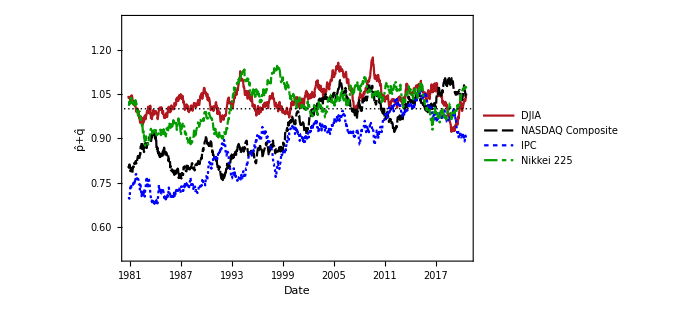

```mathematica
DateListPlot[
database[[All,"EstimatedPQSumInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂+q̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{1}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.5,1.3}}
]
```

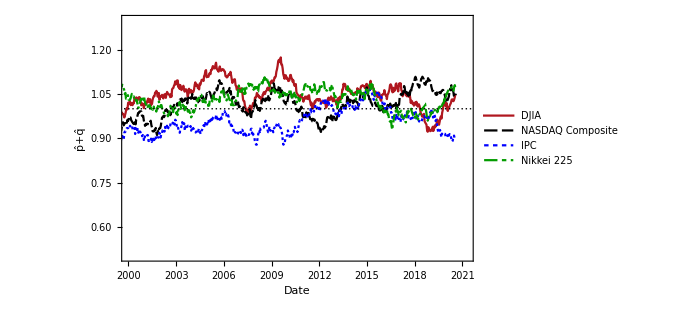

```mathematica
DateListPlot[
database[[All,"EstimatedPQSumInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂+q̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{1}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{{DateObject[{2000,1,1}],Today},{0.5,1.3}}
]
```

```mathematica
cutHistogram = Map[DeleteCases[#,{date_,_}/;date<DateObject[{2000,1,1}]]&,database[[All,"EstimatedPQSumInTime"]]];
```

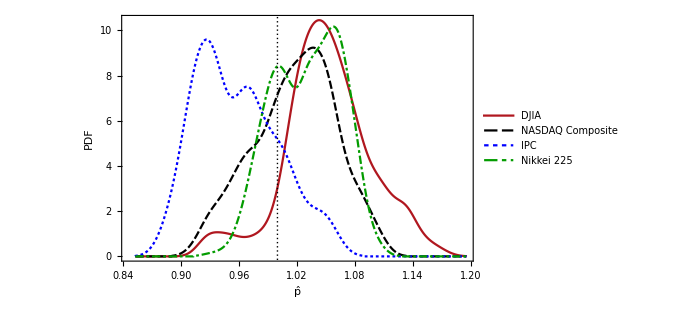

```mathematica
SmoothHistogram[cutHistogram[[All,All,2]],
PlotLegends->database[[All,"Name"]],
PlotTheme->"Monochrome", 
FrameLabel->{Style["p̂",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{1},{}},
PlotStyle->colors,
Frame->True
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],cutHistogram[[All,All,2]]]
```

| DJIA | NASDAQ Composite | IPC | Nikkei 225
μ | 1.05134±0.00197661 | 1.0176±0.00186056 | 0.957963±0.00187296 | 1.03062±0.00155486
σ | 0.0451169±0.00139902 | 0.0424273±0.00131688 | 0.0424629±0.00132567 | 0.0350448±0.00110054
Skewness | -0.186767±0.107007 | -0.249541±0.107109 | 0.448787±0.107729 | -0.189603±0.108359
Kurtosis | 3.6147±0.998112 | 2.48795±0.998108 | 2.41875±0.998086 | 2.16136±0.998064

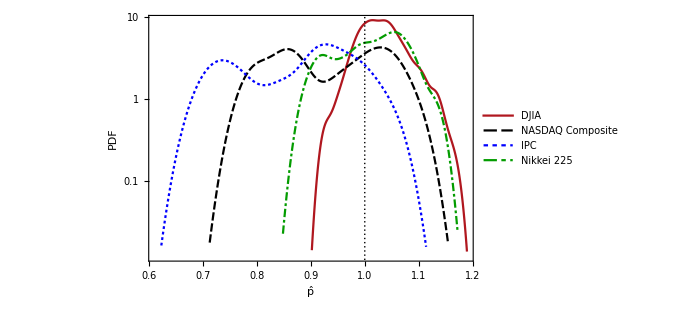

```mathematica
SmoothHistogram[database[[All,"EstimatedPQSumInTime",All,2]],
PlotLegends->database[[All,"Name"]],
PlotTheme->"Monochrome", 
FrameLabel->{Style["p̂",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{1},{}},
PlotStyle->colors,
Frame->True,
ScalingFunctions->"Log"
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"EstimatedPQSumInTime",All,2]]]
```

| DJIA | NASDAQ Composite | IPC | Nikkei 225
μ | 1.03209±0.00136967 | 0.933919±0.00304231 | 0.87499±0.00327353 | 1.01238±0.00198156
σ | 0.043464±0.000968983 | 0.0963985±0.00215231 | 0.103155±0.0023159 | 0.0620326±0.00140189
Skewness | 0.415502±0.0770753 | -0.045187±0.07719 | -0.31033±0.0776151 | -0.245387±0.0781267
Kurtosis | 3.19294±0.999015 | 1.60899±0.999012 | 1.85669±0.999002 | 2.17384±0.998988

Positive

Estimation of p for uptrends

```mathematica
AddToDataset[database,"EstimatedUpwardPInTime",EstimatePInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateUpwardGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

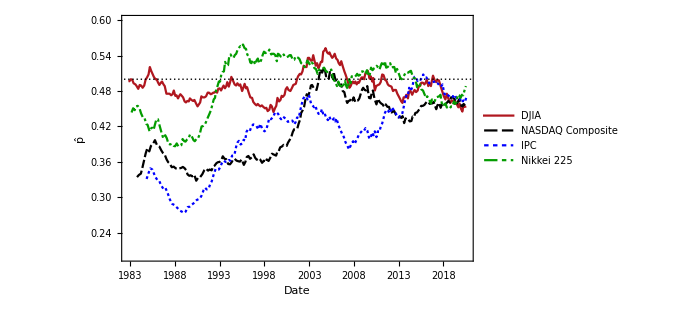

```mathematica
DateListPlot[
database[[All,"EstimatedUpwardPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.6}}
]
```

Histogram of the estimation of p in time.

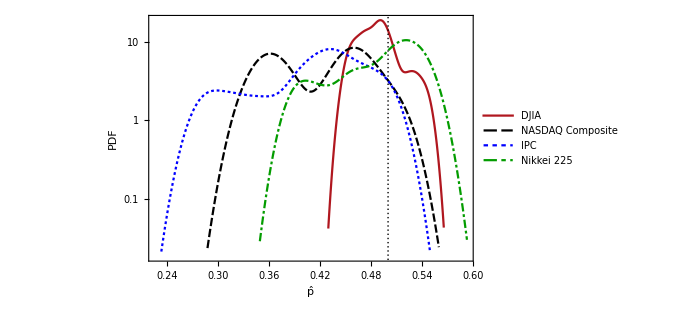

```mathematica
SmoothHistogram[database[[All,"EstimatedUpwardPInTime",All,2]],
PlotLegends->database[[All,"Name"]],
PlotTheme->"Monochrome", 
FrameLabel->{Style["p̂",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{0.5},{}},
PlotStyle->colors,
Frame->True,
ScalingFunctions->"Log"
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"EstimatedUpwardPInTime",All,2]]]
```

| DJIA | NASDAQ Composite | IPC | Nikkei 225
μ | 0.488098±0.00150471 | 0.420776±0.00370318 | 0.412899±0.00437598 | 0.4895±0.00309328
σ | 0.0236004±0.00106616 | 0.0542993±0.00262465 | 0.0615755±0.00310213 | 0.0473181±0.00219197
Skewness | 0.561129±0.155233 | -0.099901±0.165904 | -0.689135±0.172778 | -0.731292±0.159114
Kurtosis | 2.9453±0.996074 | 1.58207±0.99553 | 2.5964±0.995163 | 2.38805±0.99588

Negative

Estimation of q for downtrends

```mathematica
AddToDataset[database,"EstimatedDownwardPInTime",EstimatePInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateDownwardGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

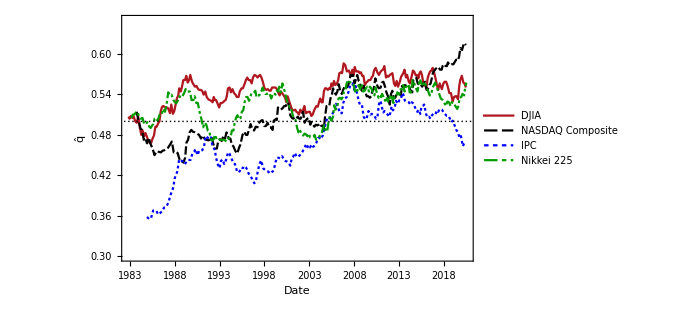

```mathematica
DateListPlot[
database[[All,"EstimatedDownwardPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["q̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.65}}
]
```

Histogram of the estimations of q in time.

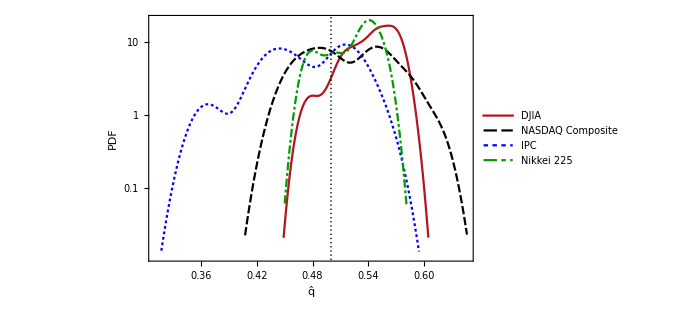

```mathematica
SmoothHistogram[database[[All,"EstimatedDownwardPInTime",All,2]],
PlotLegends->database[[All,"Name"]],
PlotTheme->"Monochrome", 
FrameLabel->{Style["q̂",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{0.5},{}},
PlotStyle->colors,
Frame->True,
ScalingFunctions->"Log"
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"EstimatedDownwardPInTime",All,2]]]
```

| DJIA | NASDAQ Composite | IPC | Nikkei 225
μ | 0.544037±0.00164298 | 0.518725±0.00291141 | 0.474116±0.00336026 | 0.523348±0.00172424
σ | 0.0256642±0.00116415 | 0.0426897±0.00206348 | 0.0471635±0.00238212 | 0.0263758±0.00122184
Skewness | -0.833793±0.15586 | 0.136965±0.165904 | -0.445233±0.17321 | -0.617614±0.159114
Kurtosis | 3.17832±0.996043 | 1.99576±0.99553 | 2.50324±0.99514 | 2.07719±0.99588

```mathematica
TrendDurationSumCountTable[market_]:=Block[{upwardDurations,downwardDurations,allDurations},
upwardDurations = UpwardTrendDuration[market["Prices"]];
downwardDurations = DownwardTrendDuration[market["Prices"]];
allDurations = DeleteDuplicates[Sort[Join[upwardDurations,downwardDurations]]];

Labeled[Grid[Prepend[Map[{#,Count[upwardDurations,#]+Count[downwardDurations,#]}&,allDurations],{"Duration","Count"}],Frame->All,Background->{None,{LightGreen}}],market["Name"],Top]
];
TrendDurationCountTable[market_,trendDurationFunction_ : TrendDuration]:=Block[{td,durations},
td = trendDurationFunction[market["Prices"]];
durations = Sort[DeleteDuplicates[td]];

Labeled[Grid[Prepend[Map[{#,Count[td,#]}&,durations],{"Duration","Count"}],Frame->All,Background->{None,{LightGreen}}],market["Name"],Top]
];
```

#### Conteo de trends

```mathematica
Labeled[Row[Map[TrendDurationCountTable[#,UpwardTrendDuration]&,database], " "],"Upward",Top]
```

Duration | Count
1 | 1262
2 | 674
3 | 354
4 | 210
5 | 90
6 | 45
7 | 23
8 | 11
9 | 5
10 | 3
11 | 2
12 | 1
13 | 1DJIADuration | Count
1 | 977
2 | 532
3 | 384
4 | 209
5 | 120
6 | 58
7 | 45
8 | 29
9 | 10
10 | 9
11 | 7
12 | 5
13 | 1
14 | 1
18 | 1
19 | 1NASDAQ CompositeDuration | Count
1 | 865
2 | 537
3 | 320
4 | 192
5 | 111
6 | 74
7 | 45
8 | 22
9 | 16
10 | 10
11 | 5
12 | 3
14 | 1
15 | 3
20 | 1IPCDuration | Count
1 | 1253
2 | 652
3 | 328
4 | 165
5 | 81
6 | 41
7 | 31
8 | 15
9 | 9
10 | 3
11 | 2
12 | 1
15 | 1
16 | 1Nikkei 225Upward

```mathematica
Labeled[Row[Map[TrendDurationCountTable[#,DownwardTrendDuration]&,database], " "],"Downward",Top]
```

Duration | Count
1 | 1429
2 | 673
3 | 316
4 | 147
5 | 70
6 | 28
7 | 10
8 | 7
12 | 1DJIADuration | Count
1 | 1240
2 | 586
3 | 300
4 | 128
5 | 71
6 | 36
7 | 13
8 | 10
9 | 4
10 | 1
16 | 1NASDAQ CompositeDuration | Count
1 | 981
2 | 559
3 | 323
4 | 151
5 | 97
6 | 42
7 | 25
8 | 8
9 | 8
10 | 4
11 | 3
12 | 1
13 | 1
19 | 1
23 | 1IPCDuration | Count
1 | 1337
2 | 644
3 | 321
4 | 164
5 | 64
6 | 27
7 | 17
8 | 4
9 | 5
12 | 1Nikkei 225Downward

```mathematica
Labeled[Row[Map[TrendDurationSumCountTable,database], " "],"Upward+Downward",Top]
```

Duration | Count
1 | 2691
2 | 1347
3 | 670
4 | 357
5 | 160
6 | 73
7 | 33
8 | 18
9 | 5
10 | 3
11 | 2
12 | 2
13 | 1DJIADuration | Count
1 | 2217
2 | 1118
3 | 684
4 | 337
5 | 191
6 | 94
7 | 58
8 | 39
9 | 14
10 | 10
11 | 7
12 | 5
13 | 1
14 | 1
16 | 1
18 | 1
19 | 1NASDAQ CompositeDuration | Count
1 | 1846
2 | 1096
3 | 643
4 | 343
5 | 208
6 | 116
7 | 70
8 | 30
9 | 24
10 | 14
11 | 8
12 | 4
13 | 1
14 | 1
15 | 3
19 | 1
20 | 1
23 | 1IPCDuration | Count
1 | 2590
2 | 1296
3 | 649
4 | 329
5 | 145
6 | 68
7 | 48
8 | 19
9 | 14
10 | 3
11 | 2
12 | 2
15 | 1
16 | 1Nikkei 225Upward+Downward

```mathematica
Labeled[Row[Map[TrendDurationCountTable[#,TrendDuration]&,database], " "],"All",Top]
```

Duration | Count
1 | 2691
2 | 1347
3 | 670
4 | 357
5 | 160
6 | 73
7 | 33
8 | 18
9 | 5
10 | 3
11 | 2
12 | 2
13 | 1DJIADuration | Count
1 | 2217
2 | 1118
3 | 684
4 | 337
5 | 191
6 | 94
7 | 58
8 | 39
9 | 14
10 | 10
11 | 7
12 | 5
13 | 1
14 | 1
16 | 1
18 | 1
19 | 1NASDAQ CompositeDuration | Count
1 | 1846
2 | 1096
3 | 643
4 | 343
5 | 208
6 | 116
7 | 70
8 | 30
9 | 24
10 | 14
11 | 8
12 | 4
13 | 1
14 | 1
15 | 3
19 | 1
20 | 1
23 | 1IPCDuration | Count
1 | 2590
2 | 1296
3 | 649
4 | 329
5 | 145
6 | 68
7 | 48
8 | 19
9 | 14
10 | 3
11 | 2
12 | 2
15 | 1
16 | 1Nikkei 225All

# Waiting time analysis

We can model waiting times as the number of failures (days without observing the desired trend duration) in a sequence of trials (days passed) with probability of sucess p. This is also a geometric distribution.

Distribution

Smooth histogram

```mathematica
DayLegends[n_Integer]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
Range[n]
];
DayLegends[l_List]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
l
];

WaitTime[prices_,duration_]:=Block[{td,grouped,dayIntervals},
td = TrendDuration[prices];
grouped = Drop[Split[td,#≠duration&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
WaitTimeForRuns[prices_,range_:4]:=Map[WaitTime[prices,#]&,Range[range]];

WaitTimeForMarket[market_]:=Block[{dist},
dist =WaitTimeForRuns[market["Prices"]];
SmoothHistogram[dist,1,
PlotRange->{{0,50},All},
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait",bigFontSize],Style["PDF",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]
];
```

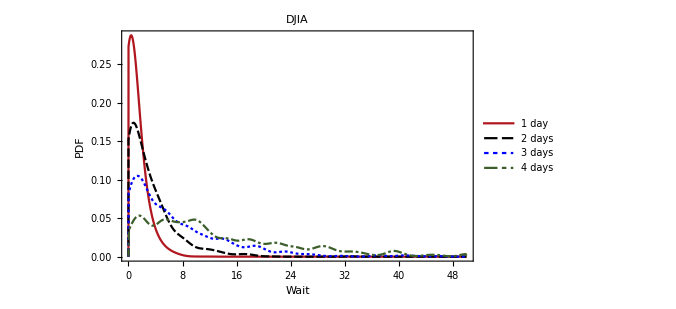
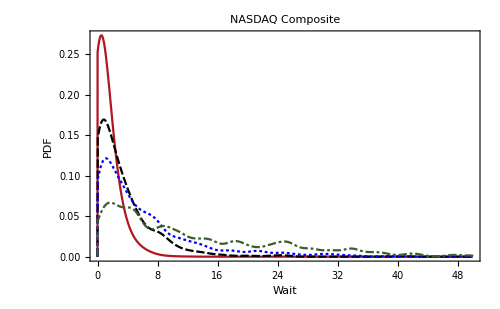
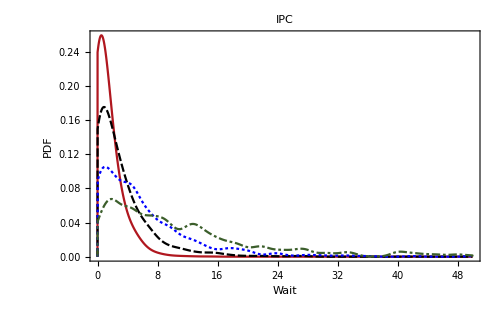
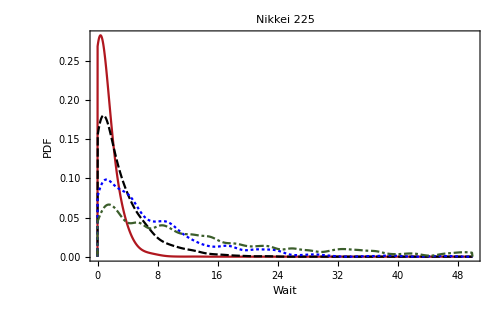

```mathematica
Map[WaitTimeForMarket,database]
```

Discrete

```mathematica
HistogramPoints[data_]:=SortBy[Map[{#,N@(Count[data,#]/Length[data])}&,DeleteDuplicates[data]],First];
GenerateFitted[p_,max_]:=Table[{k,PDF[GeometricDistribution[p],k]},{k,0,max}];
DiscreteHistogramWaitTime[market_]:=Block[{waitTimes,histogramPts,ps,legend,fitted},
waitTimes = WaitTimeForRuns[market["Prices"]];
histogramPts = Map[HistogramPoints,waitTimes];
ps = Map[EstimateP,waitTimes];
legend = MapThread[StringJoin[#1,", p̂ = ",ToString[#2]]&,{DayLegends[4],ps}];
fitted = Map[GenerateFitted[#,70]&,ps];

ListLogPlot[
Join[fitted,histogramPts],
Joined->{True,True,True,True,False,False,False,False},
PlotRange->{{0,70},{10^-5,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[legend,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
]
];
```

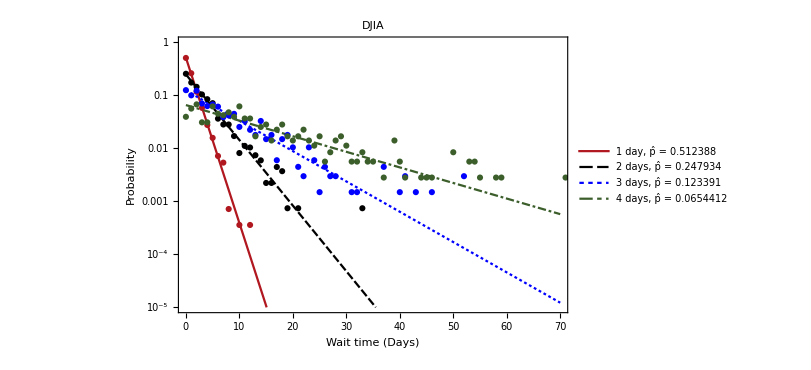
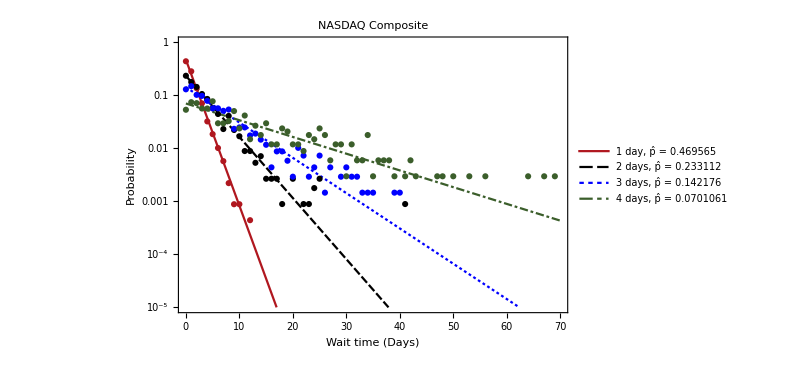
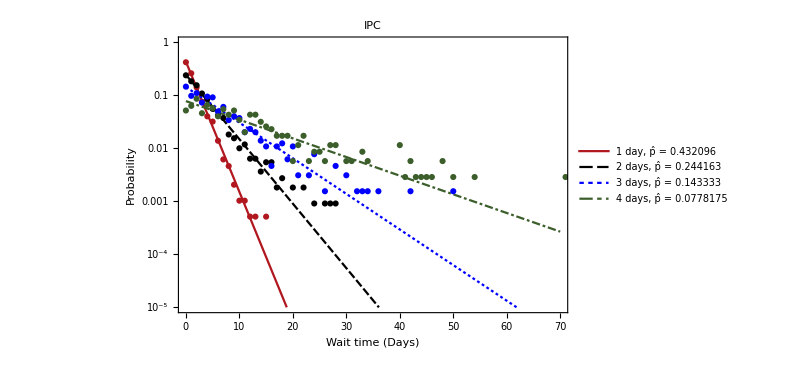
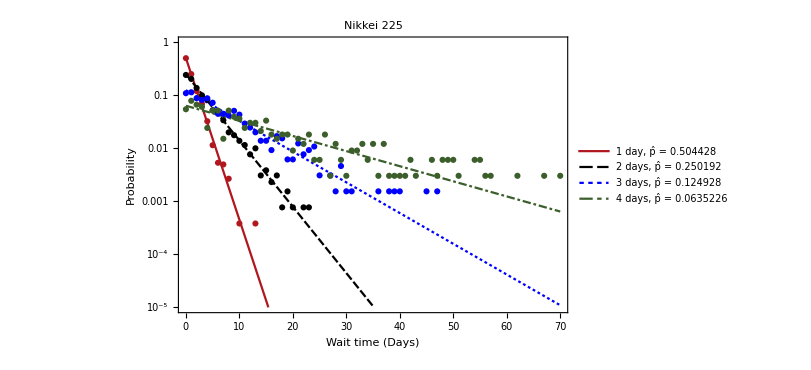

```mathematica
Map[DiscreteHistogramWaitTime,database]
```

Test for a geometric distribution

```mathematica
WaitTimeGOF[market_]:=Block[{dist,testData},
dist = Map[WaitTime[market,#]&,Range[4]];
testData = MapThread[{GeometricDistribution[#2],PearsonChiSquareTest[#1,GeometricDistribution[#2]]}&,{dist,{0.5,0.25,0.125,0.0625}}];

Labeled[
Grid[
Prepend[testData,{"Hypothesis","p-value"}],
Dividers->{{False,True},{False,True}}
],
market["Name"],
Top
]
];
```

In time

```mathematica
RunDistributionInTime[market_,window_,skip_]:=DynamicModule[{part,hs},
part = Partition[market["Prices"],window,skip];
hs = Map[
SmoothHistogram[
WaitTimeForRuns[#,3],1,
PlotRange->{{0,50},{0,0.30}},
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait",bigFontSize],Style["PDF",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[3],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1}]
];

GeneratePointsAndFit[prices_]:=Block[{waitTimes,histogramPts,ps,legend,fitted},
waitTimes = WaitTimeForRuns[prices];
histogramPts = Map[HistogramPoints,waitTimes];
ps = Map[EstimateP,waitTimes];
legend = MapThread[StringJoin[#1,", p̂ = ",ToString[#2]]&,{DayLegends[4],ps}];
fitted = Map[GenerateFitted[#,70]&,ps];

{Join[fitted,histogramPts],legend}
];
DiscreteHistogramWaitTimeEvolution[market_,window_,skip_]:=DynamicModule[{part,legend,data,hs},
part = Partition[market["Prices"],window,skip];

hs = Map[
({data,legend} = GeneratePointsAndFit[#];
ListLogPlot[
data,
Joined->{True,True,True,True,False,False,False,False},
PlotRange->{{0,70},{10^-15,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[legend,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
])&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1},SaveDefinitions->True]
];
```

```mathematica
Map[DiscreteHistogramWaitTimeEvolution[#,2000,200]&,database]
```

### More detailed view

```mathematica
GeneratePointsAndFit2[prices_]:=Block[{waitTimes,histogramPts,p,legend,fitted},
waitTimes = WaitTime[prices,1];
histogramPts = HistogramPoints[waitTimes];
p = EstimateP[waitTimes];
legend = StringJoin["p̂ = ",ToString[p]];
fitted = GenerateFitted[p,70];

{{histogramPts,fitted},legend}
];
DiscreteHistogramWaitTimeEvolution2[market_,window_,skip_]:=DynamicModule[{part,ref,legend,data,hs},
part = Partition[market["Prices"],window,skip];
ref = GenerateFitted[0.5,16];

hs = Map[
({data,legend} = GeneratePointsAndFit2[#];
ListLogPlot[
Join[data,{ref}],
Joined->{False,True,True},
PlotRange->{{0,16},{10^-7,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[{"Data","Fit: "<>legend,"p̂ = 0.5"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
])&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1}]
]
```

```mathematica
Map[DiscreteHistogramWaitTimeEvolution2[#,2000,200]&,database]
```

Observación: Tanto el IPC como NASDAQ presentan periodos en los que transcurre una cantidad de días hasta que se vuelve a presentar un run de 1 día que es mayor que la esperada asumiendo la hipótesis nula de caminata aleatoria.

Estimate in time

```mathematica
EstimatePRunsEvolution[market_,duration_,window_,skip_]:=Block[{part,datesPart,hs,p},
part = Partition[market["Prices"],window,skip];
datesPart = Partition[market["Dates"],window,skip];
hs = Map[WaitTime[#,duration]&,part];

MapThread[{Last[#1],p/.FindDistributionParameters[#2,GeometricDistribution[p]]}&,{datesPart,hs}]
];
PlotPRunsEvolution[market_,window_,skip_]:=Block[{ps},
ps = Map[EstimatePRunsEvolution[market,#,window,skip]&,Range[3]];
DateListPlot[ps,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5,0.25,0.125}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotLabel->market["Name"],
PlotLegends->If[market["Name"]=="DJIA",Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],None]
]
];
```

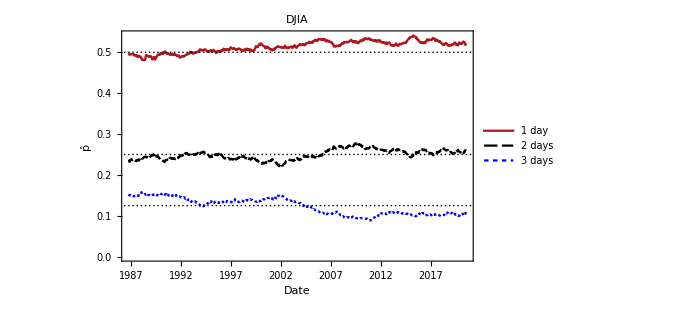
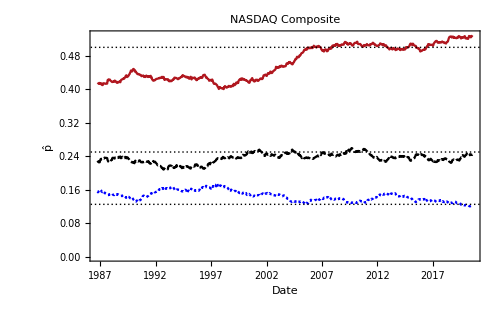
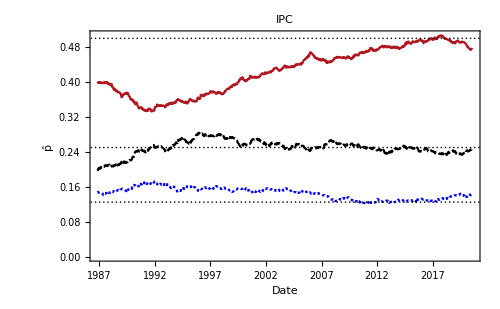
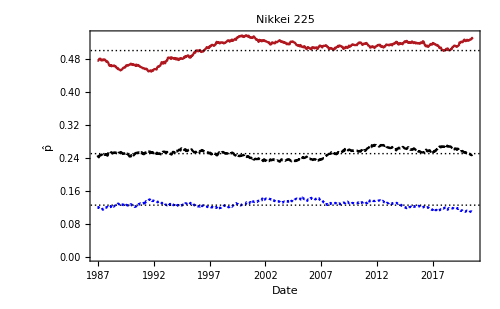

```mathematica
Map[PlotPRunsEvolution[#,2000,10]&,database]
```

One day trends are possibly the cause of deviations from the random walk.

Test in time

```mathematica
HypothesisGOF[wt_]:=MapThread[PearsonChiSquareTest[#1,GeometricDistribution[#2]]&,{wt,{0.5,0.25,0.125}}];
RunDistributionHypothesisGOFInTime[market_,window_,skip_]:=Block[{part,hs,pvalues},
part = Partition[market["Prices"],window,skip];
hs = Map[WaitTimeForRuns[#,3]&,part];
pvalues = Transpose[Map[HypothesisGOF,hs]];

DateListLogPlot[
pvalues,
{market["Dates"][[2000]],market["Dates"][[-1]]},
PlotLegends->If[market["Name"]=="DJIA",Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],None],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p-Value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0,1}},
Frame->True,
PlotLabel->market["Name"],
GridLines->{{},{0.01,0.05,0.1}}
]
];
```

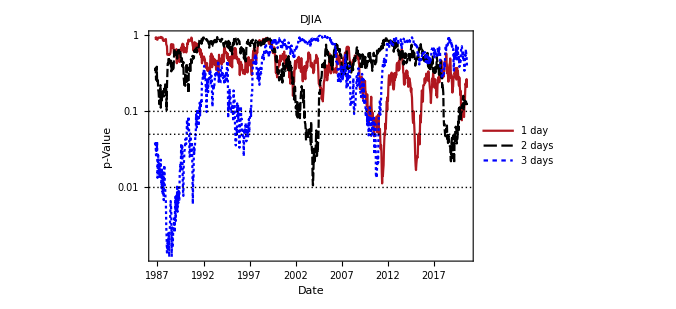
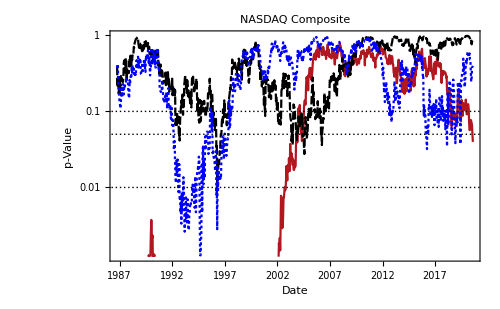
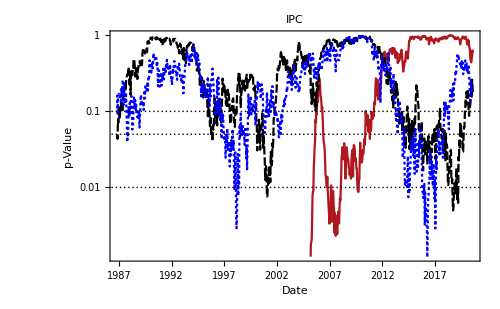
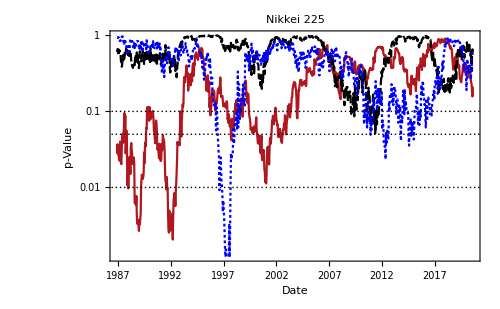

```mathematica
Map[RunDistributionHypothesisGOFInTime[#,2000,10]&,database]
```

Directional wait time estimation

```mathematica
SignedTrendDuration[prices_] := Map[First[#]*Length[#]&, Split[Sign[Returns[prices]]]];
UpwardWaitTime[prices_,duration_]:=Block[{td,grouped,dayIntervals},
td = SignedTrendDuration[prices];
grouped = Drop[Split[td,#≠duration&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
DownwardWaitTime[prices_,duration_]:=Block[{td,grouped,dayIntervals},
td =SignedTrendDuration[prices];
grouped = Drop[Split[td,#≠(-duration)&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
WaitTime[prices_,duration_,"Upward"]:=UpwardWaitTime[prices,duration];
WaitTime[prices_,duration_,"Downward"]:=DownwardWaitTime[prices,duration];

EstimatePRunsEvolutionDirectional[market_,window_,skip_,direction_,duration_ :1]:=Block[{part,datesPart,hs,p},
part = Partition[market["Prices"],window,skip];
datesPart = Partition[market["Dates"],window,skip];
hs = Map[WaitTime[#,duration,direction]&,part];

MapThread[{Last[#1],p/.FindDistributionParameters[#2,GeometricDistribution[p]]}&,{datesPart,hs}]
];
PlotPRunsEvolutionDirectional[market_,window_,skip_,duration_ :1]:=Block[{pUpward,pDownward},
pUpward = EstimatePRunsEvolutionDirectional[market,window,skip,"Upward",duration];
pDownward = EstimatePRunsEvolutionDirectional[market,window,skip,"Downward",duration];

DateListPlot[{pUpward,pDownward},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{dateObjects,{0.5,0.25,0.125,0.0625}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotLabel->market["Name"],
PlotLegends->Placed[LineLegend[{"Upward","Downward"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],
PlotRange->{Automatic,{0,0.5}}
]
];
```

### 1 day

Nota: Hay correlación entre la estimación p de los tiempos de espera de 1 día con la duración de los trends.

```mathematica
Map[PlotPRunsEvolutionDirectional[#,2000,10,1]&,database]
```

### 2 days

```mathematica
Map[PlotPRunsEvolutionDirectional[#,2000,10,2]&,database]
```

### 3 days

```mathematica
Map[PlotPRunsEvolutionDirectional[#,2000,10,3]&,database]
```

## Record breaking statistic

```mathematica
PlotRecordStatisticForWT[market_]:=Block[{waitTimeRecords},
waitTimeRecords = Map[GetRecordTimes,WaitTimeForRuns[market["Prices"]]];

ListLinePlot[waitTimeRecords,
PlotRange->All,
PlotLegends->Placed[LineLegend[DayLegends[4],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Time",15], Style["Record value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->market["Name"],
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.65}},
Frame->True,
PlotMarkers->{Automatic, 10}
]
];
```

```mathematica
RecordStatisticTestForWT[market_,window_ :50]:=Block[{ρ,waitingTimeRecords,results,txtresults,param,grid},
waitingTimeRecords = Map[GetWindowedRecordTimes[#,window]&,WaitTimeForRuns[market["Prices"],3]];
results = Map[PearsonChiSquareTest[#,ZipfDistribution[window,ρ]]&,waitingTimeRecords];
txtresults = Map[PearsonChiSquareTest[#,ZipfDistribution[window,ρ],"ShortTestConclusion"]&,waitingTimeRecords];
param = Map[ZipfDistribution[window,ρ]/.FindDistributionParameters[#,ZipfDistribution[window,ρ]]&,waitingTimeRecords];

grid = Grid[Prepend[Thread[{DayLegends[3],param,results,txtresults}],{"Length","Distribution","p-value","Result"}],Frame->True];
Labeled[grid,market["Name"],Top]
];

HistogramPointPlotForWT[{data1_,data2_,data3_},opts: OptionsPattern[]]:=Block[
{
pltData1 = HistogramPoints[data1], 
pltData2 = HistogramPoints[data2],
pltData3 = HistogramPoints[data3]
},

ListPlot[
{pltData1,pltData1,pltData2,pltData2,pltData3,pltData3},
Joined->{False,True,False,True,False,True},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{colors[[1]],{PointSize[Large],colors[[1]]},colors[[2]],{PointSize[Large],colors[[2]]},colors[[3]],{PointSize[Large],colors[[3]]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[Flatten[Thread[{DayLegends[3],DayLegends[3]}]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],
FilterRules[{opts},Options[ListPlot]]
]
];
HistogramPointPlotForWT[market_,opts: OptionsPattern[]]:=Block[{data},
data = Map[GetWindowedRecordTimes[#,10,1]&,WaitTimeForRuns[market["Prices"],3]];
HistogramPointPlotForWT[data,PlotLabel->market["Name"],ScalingFunctions->"Log",PlotRange->All,opts]
];
```

Drop::drop: Cannot drop positions 1 through 1 in {}.

Drop::drop: Cannot drop positions -1 through -1 in {}.

Drop::drop: Cannot drop positions 1 through 1 in {}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

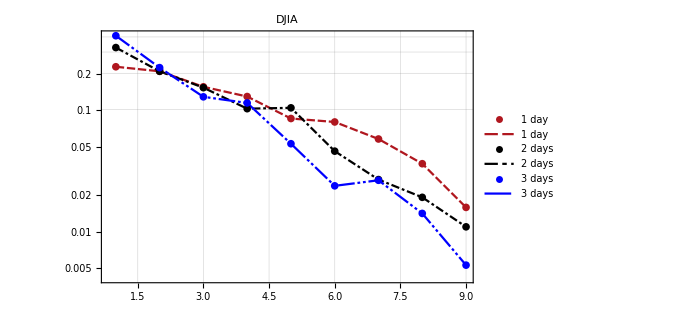
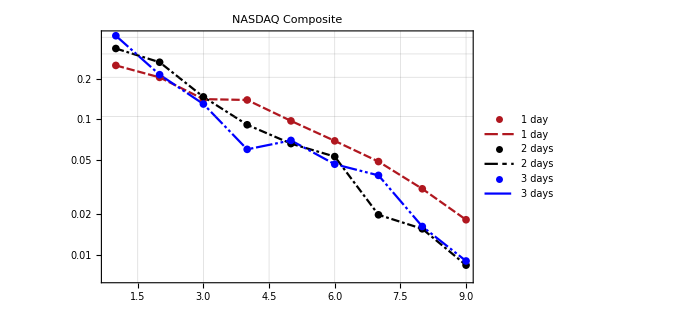
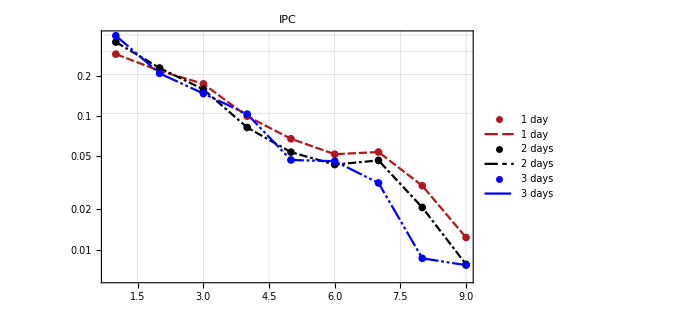
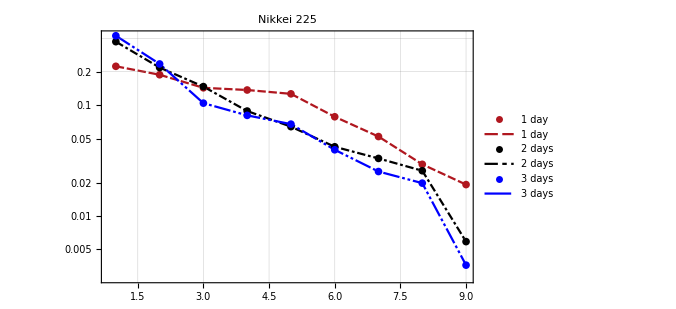

```mathematica
Map[HistogramPointPlotForWT,database]
```